# Use Machine Learning to Predict if Topography is Land or Ocean

Nguyen Minh Khang
Mentor: Harshal Gajjar
12th July 2019, Boston

## Project Description

Topography is the arrangement of the natural and artificial physical features of an arbitrary area and the goal of the project is trying to predict if a given topography is on land or under water (in an ocean). First, I have to scrape a bunch of data of various topography of each different location on Earth, which may be on land or may be deep in the sea. Thus, I plan to use machine learning to do the classification and on the way explore other algorithms and features that could improve accuracy.

## Collecting Data

Scraping on-land Data

Create a list of Capital Cities:

```mathematica
capitalcities = DeleteMissing[EntityValue[EntityClass["Country","Countries"],"CapitalCity"]]//Flatten;
```

Take some of them:

```mathematica
capitalcities=Take[capitalcities,50];
```

Do the same process on other lists (buildings, mountains, cities):

```mathematica
buildings =EntityList["Building"];
```

```mathematica
buildings=Take[buildings,-50];
```

```mathematica
mountains = MountainData[All];
```

```mathematica
mountains = Take[mountains,50];
```

```mathematica
cities = EntityList["City"]//Flatten;
```

```mathematica
cities = Take[cities,-50]'
```

Scraping under-water Data

```mathematica
underseafeatures=DeleteMissing[EntityValue[EntityClass["Ocean","Seas"],"UnderseaFeatures"]]//Flatten;
```

```mathematica
underseafeatureslist = Take[underseafeatures,-200];
```

## Image Processing

Image Processing

Observation : I saw that the land surface images are a little bit spiky and ocean surface images are smoother , let’s try to find out a way to programmatically figure out these differences!

Convert 3D Plot into a 2D Relief Plot in Black and White Theme:

```mathematica
capitalcitieselevationPlots=ReliefPlot[Reverse[GeoElevationData[#,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@capitalcities;
```

Generating a final list of images which represent the dilation of the differences between the 2D Relief Plot above and its blurred:

```mathematica
finalcapitalcitieslist=Dilation[ImageDifference[Blur[#,20],#],10]&/@capitalcitieselevationPlots;
```

A sample of the final list of images:

```mathematica
RandomSample[finalcapitalcitieslist,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do the same process on other packages:

```mathematica
buildingselevationPlots=ReliefPlot[Reverse[GeoElevationData[#,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@buildings;
```

```mathematica
finalbuildingslist=Dilation[ImageDifference[Blur[#,20],#],10]&/@buildingselevationPlots;
```

```mathematica
RandomSample[finalbuildingslist,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mountainselevationPlots=ReliefPlot[Reverse[GeoElevationData[#,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@mountains;
```

```mathematica
finalmountainslist=Dilation[ImageDifference[Blur[#,20],#],10]&/@mountainselevationPlots;
```

```mathematica
RandomSample[finalmountainslist,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
citieselevationPlots=ReliefPlot[Reverse[GeoElevationData[#,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@cities;
```

```mathematica
finalcitieslist = Dilation[ImageDifference[Blur[#,20],#],10]&/@citieselevationPlots;
```

```mathematica
RandomSample[finalcitieslist,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
underseafeatureselevationPlots= ReliefPlot[Reverse[GeoElevationData[#,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@underseafeatureslist;
```

```mathematica
finalunderseafeatureslist = Dilation[ImageDifference[Blur[#,20],#],10]&/@underseafeatureselevationPlots
```

```mathematica
RandomSample[finalunderseafeatureslist,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Another Proposal

My mentor Mr. Harshal gave me a nice approaching to solve this Image Processing Step, which is using Discrete Fourier Transformation to convert an image into a matrix. However, we realized that there is a problem ibut the problem was that all Fourier images were very similar!

Generate Black and White Relief Plots of Mount Everest and Mariana Trench:

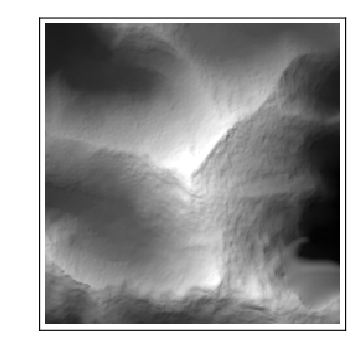

```mathematica
mountain=ReliefPlot[Reverse[GeoElevationData[Entity["Mountain","MountEverest"],GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel]
```

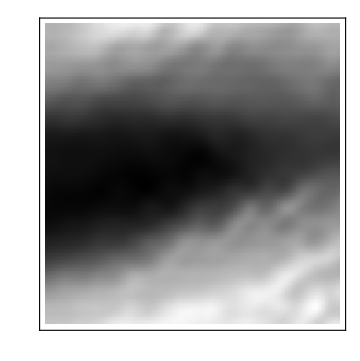

```mathematica
trench=ReliefPlot[Reverse[GeoElevationData[LinguisticAssistant,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel]
```

```mathematica
data=ImageData[trench];
{nRow,nCol,nChannel}=Dimensions[data];
d=data[[All,All,2]];
d=d*(-1)^Table[i+j,{i,nRow},{j,nCol}];
fw=Fourier[d,FourierParameters->{1,1}];
```

```mathematica
fw;
```

```mathematica
Image[(#/Max@#)&@Log[1+Abs[fw]]]
```

-Graphics-

```mathematica
data2=ImageData[mountain];
{nRow,nCol,nChannel}=Dimensions[data2];
d=data2[[All,All,2]];
d=d*(-1)^Table[i+j,{i,nRow},{j,nCol}];
fw=Fourier[d,FourierParameters->{1,1}];
Image[(#/Max@#)&@Log[1+Abs[fw]]]
```

-Graphics-

```mathematica
Table[i+j,{i,nRow},{j,nCol}];
```

## Creating Training Set

Gather all the final lists on-land objects:

```mathematica
finalonlandlist=Join[finalcapitalcitieslist,finalcitieslist,finalbuildingslist,finalmountainslist];
```

Gather all the final lists under-water objects:

```mathematica
finalunderseafeatureslist = finalunderseafeatureslist
```

Creating the training set:

```mathematica
finaltraininglist=Join[finalonlandlist,finalunderseafeatureslist]
```

A sample of the training set:

```mathematica
RandomSample[finaltraininglist,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Checking

Checking

```mathematica
FeatureSpacePlot[finaltraininglist]
```

-Graphics-

## Generating Classify Function

Creating Classify Function with the training set and also the result of each elements in the set

```mathematica
landExamplesAndClasses=(#-> "Land"&)/@finalonlandlist;
seaExamplesAndClasses=(#-> "Sea"&)/@finalunderseafeatureslist;
```

```mathematica
predict=Classify[Union[landExamplesAndClasses,seaExamplesAndClasses]]
```

ClassifierFunction[…]

## Input and Output

```mathematica
topography=GeoElevationData[LinguisticAssistant,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic];
```

```mathematica
topography
```

QuantityArray[…]

```mathematica
predict[Dilation[ImageDifference[Blur[ReliefPlot[Reverse[topography],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None],20],ReliefPlot[Reverse[topography],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]],10]]
```

Sea

## Creating the Final Function to Return Probabilities

Creating the final function return probabilities as an image arguments:

```mathematica
predictor[img_]:=predict[Dilation[ImageDifference[Blur[img,20],img],10],"Probabilities"]//Normal
```

Testing by plugging a topography of Philippines Trench:

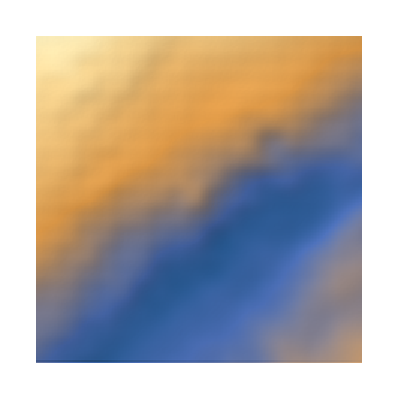

```mathematica
test=ReliefPlot[topography,Frame->False,PlotRangePadding->None]
```

```mathematica
predictor[-Graphics-]
```

{Land→0.0672905,Sea→0.932709}

## An Application: “Generating Temperature Map and Smooth Plot”

Choose a random place:

```mathematica
position = Entity["City",{"LosAngeles","California","UnitedStates"}];
```

Temperature Map in Minor Scale:

Try to make a Temperature Map in a Minor Scale of the chosen location:

From the located position, move to its right 8000 meters in each step to get a list of new coordinates:

```mathematica
pos = Table[GeoDestination[GeoPosition[position],{dist,90}],{dist,0,24000,8000}]
```

{GeoPosition[{34.0194,-118.411}],GeoPosition[{34.0194,-118.324}],GeoPosition[{34.0193,-118.238}],GeoPosition[{34.0191,-118.151}]}

From the list of new coordinates above, move downwards 8000 meters in each step to get another list of new coordinates:

```mathematica
pos2 = Table[GeoDestination[GeoPosition[#],{dist,180}],{dist,0,16000,8000}]&/@pos
```

{{GeoPosition[{34.0194,-118.411}],GeoPosition[{33.9473,-118.411}],GeoPosition[{33.8751,-118.411}]},{GeoPosition[{34.0194,-118.324}],GeoPosition[{33.9472,-118.324}],GeoPosition[{33.8751,-118.324}]},{GeoPosition[{34.0193,-118.238}],GeoPosition[{33.9471,-118.238}],GeoPosition[{33.875,-118.238}]},{GeoPosition[{34.0191,-118.151}],GeoPosition[{33.947,-118.151}],GeoPosition[{33.8749,-118.151}]}}

Join two lists above together:

```mathematica
pos3 = Join[pos,pos2]//Flatten
```

{GeoPosition[{34.0194,-118.411}],GeoPosition[{34.0194,-118.324}],GeoPosition[{34.0193,-118.238}],GeoPosition[{34.0191,-118.151}],GeoPosition[{34.0194,-118.411}],GeoPosition[{33.9473,-118.411}],GeoPosition[{33.8751,-118.411}],GeoPosition[{34.0194,-118.324}],GeoPosition[{33.9472,-118.324}],GeoPosition[{33.8751,-118.324}],GeoPosition[{34.0193,-118.238}],GeoPosition[{33.9471,-118.238}],GeoPosition[{33.875,-118.238}],GeoPosition[{34.0191,-118.151}],GeoPosition[{33.947,-118.151}],GeoPosition[{33.8749,-118.151}]}

Make all 4kmx4km -sized plots from the list of coordinates above:

```mathematica
plotstest=ReliefPlot[Reverse[GeoElevationData[{#,{(#/.GeoPosition[x_]->x)[[1]]-0.05,(#/.GeoPosition[x_]->x)[[2]]+0.05}},GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic,GeoCenter->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@(GeoPosition/@pos3)
```

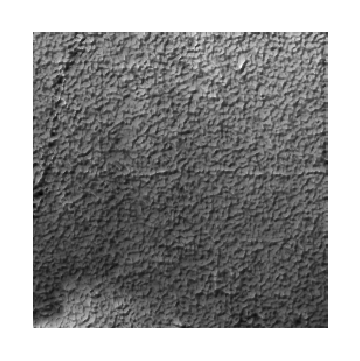
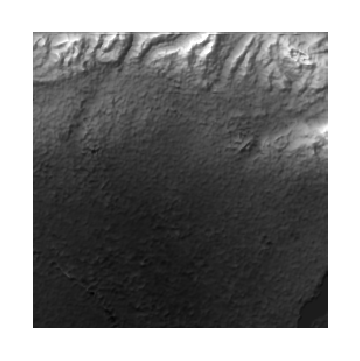
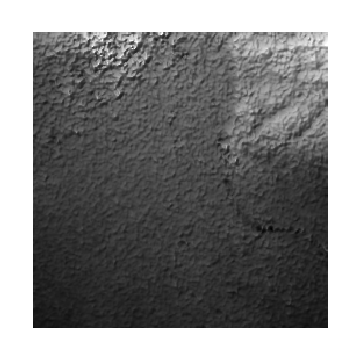

```mathematica
RandomSample[plotstest,3]
```

For each plot, apply the Final Function the get the Probability of Land and Water:

```mathematica
topographies1=predictor[#]&/@plotstest//Flatten
```

{Land→0.973609,Sea→0.0263913,Land→0.953273,Sea→0.0467271,Land→0.947274,Sea→0.052726,Land→0.984118,Sea→0.0158823,Land→0.973609,Sea→0.0263913,Land→0.990255,Sea→0.00974523,Land→0.97304,Sea→0.0269601,Land→0.953273,Sea→0.0467271,Land→0.971853,Sea→0.0281473,Land→0.971966,Sea→0.0280345,Land→0.947274,Sea→0.052726,Land→0.990649,Sea→0.00935114,Land→0.98383,Sea→0.0161696,Land→0.984118,Sea→0.0158823,Land→0.990252,Sea→0.00974799,Land→0.971579,Sea→0.0284209}

Collect all the Land Probability of each plot and Arrange them into a 4x4-sized matrix  :

```mathematica
plotnew=Partition[Values[topographies1][[#]]&/@Flatten[Position[Keys[topographies1],"Land"]],4]
```

{{0.973609,0.953273,0.947274,0.984118},{0.973609,0.990255,0.97304,0.953273},{0.971853,0.971966,0.947274,0.990649},{0.98383,0.984118,0.990252,0.971579}}

From the mini matrix, convert each number into Thermometer Colors ranging from - 0,5 to 0.5:

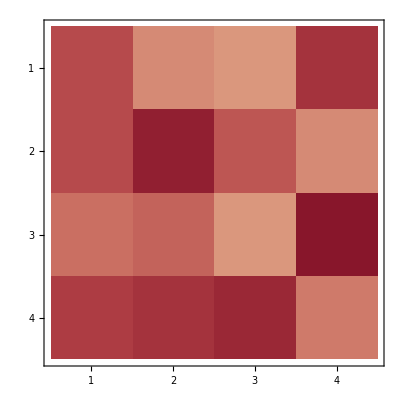

```mathematica
MatrixPlot[plotnew-.5,ColorFunction->ColorData["ThermometerColors"]]
```

Temperature Map in an Extremely Large Scale:

Make a bigger Temperature Map :

I was trying to create a Temperature Map of a country, for instance, Japan. But I figured out that my computer does not want to do this TvT.

Get all coordinates from the chosen location:

```mathematica
position1 = LinguisticAssistant
```

```mathematica
coordinates=position1["FullCoordinates"]
```

Get the longitudes and latitudes  of the points treating an imaginary box that wrap up the chosen location:

```mathematica
getcoor = MinMax/@Transpose[Cases[coordinates,{_,_},∞]]//Flatten
```

Create the coordinates of the 4 vertices of the box:

```mathematica
pt1 = {getcoor[[1]],getcoor[[3]]}
```

```mathematica
pt2 = {getcoor[[2]],getcoor[[4]]}
```

```mathematica
pt3 = {getcoor[[1]],getcoor[[4]]}
```

```mathematica
pt4 = {getcoor[[2]],getcoor[[3]]}
```

Calculate the width of the box and convert it into kilometers:

```mathematica
width=UnitConvert[GeoDistance[pt1,pt3],LinguisticAssistant]//QuantityMagnitude
```

Calculate the length of box and convert it into kilometers:

```mathematica
length=UnitConvert[GeoDistance[pt3,pt2],LinguisticAssistant]//QuantityMagnitude
```

From point 4, move to its right 8000 meters in each step to get a list of new coordinates:

```mathematica
poswidth=Table[GeoDestination[GeoPosition[pt4],{dist,90}],{dist,0,width,8000}]
```

From the list of new coordinates above, move downwards 8000 meters in each step to get another list of new coordinates:

```mathematica
poslength=Table[GeoDestination[GeoPosition[#],{dist,180}],{dist,0,length,8000}]&/@poswidth
```

Join all coordinates together:

```mathematica
allpos = Join[poswidth,poslength]//Flatten
```

Make a list of plots for each coordinate in the list above:

```mathematica
plots=ReliefPlot[Reverse[GeoElevationData[{#,{(#/.GeoPosition[x_]->x)[[1]]-0.05,(#/.GeoPosition[x_]->x)[[2]]+0.05}},GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic,GeoCenter->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@(GeoPosition/@allpos)
```

For each plot, apply the Final Function the get the Probability of Land and Water:

```mathematica
topographiesbigscale=predictor[#]&/@plots//Flatten
```

Find the width of the preferred matrix  to re-arrange the numbers into a matrix:

```mathematica
matrixwidth=Table[n, {n, 0, width, 8000}] // Length
```

Collect all the Land Probability of each plot and Arrange them into a  big matrix  :

```mathematica
plotnou=Partition[Values[topographiesbigscale][[#]]&/@Flatten[Position[Keys[topographiesbigscale],"Land"]],matrixwidth]
```

From the big matrix, convert each number into Thermometer Colors ranging from - 0,5 to 0.5:

```mathematica
MatrixPlot[plotnou-.5,ColorFunction->ColorData["ThermometerColors"]]
```

Temperature Map in Medium Scale:

Because I can not generate an extremely large temperature map so I came up with a medium sized temperature map would be better:

Get the coordinates of current location:

```mathematica
vitri=GeoPosition[Here]
```

GeoPosition[{42.37,-71.23}]

From current location, move to its right 15 times for 8000 meters in each step to get a list of new coordinates:

```mathematica
vitringang=Table[GeoDestination[GeoPosition[vitri],{dist,90}],{dist,0,120000,8000}]
```

{GeoPosition[{42.37,-71.23}],GeoPosition[{42.37,-71.1329}],GeoPosition[{42.3698,-71.0358}],GeoPosition[{42.3696,-70.9386}],GeoPosition[{42.3693,-70.8415}],GeoPosition[{42.369,-70.7444}],GeoPosition[{42.3685,-70.6473}],GeoPosition[{42.368,-70.5501}],GeoPosition[{42.3674,-70.453}],GeoPosition[{42.3667,-70.3559}],GeoPosition[{42.3659,-70.2588}],GeoPosition[{42.365,-70.1617}],GeoPosition[{42.3641,-70.0646}],GeoPosition[{42.363,-69.9675}],GeoPosition[{42.3619,-69.8704}],GeoPosition[{42.3607,-69.7733}]}

From each coordinate in the list above, move downwards 15 times for 8000 meters in each step to get a list of new coordinates:

```mathematica
vitridoc= Table[GeoDestination[GeoPosition[#],{dist,180}],{dist,8000,120000,8000}]&/@vitringang
```

{{GeoPosition[{42.298,-71.23}],GeoPosition[{42.226,-71.23}],GeoPosition[{42.1539,-71.23}],GeoPosition[{42.0819,-71.23}],GeoPosition[{42.0099,-71.23}],GeoPosition[{41.9379,-71.23}],GeoPosition[{41.8658,-71.23}],GeoPosition[{41.7938,-71.23}],GeoPosition[{41.7218,-71.23}],GeoPosition[{41.6498,-71.23}],GeoPosition[{41.5777,-71.23}],GeoPosition[{41.5057,-71.23}],GeoPosition[{41.4337,-71.23}],GeoPosition[{41.3616,-71.23}],GeoPosition[{41.2896,-71.23}]},{GeoPosition[{42.2979,-71.1329}],GeoPosition[{42.2259,-71.1329}],GeoPosition[{42.1539,-71.1329}],GeoPosition[{42.0819,-71.1329}],GeoPosition[{42.0098,-71.1329}],GeoPosition[{41.9378,-71.1329}],GeoPosition[{41.8658,-71.1329}],GeoPosition[{41.7938,-71.1329}],GeoPosition[{41.7217,-71.1329}],GeoPosition[{41.6497,-71.1329}],GeoPosition[{41.5777,-71.1329}],GeoPosition[{41.5057,-71.1329}],GeoPosition[{41.4336,-71.1329}],GeoPosition[{41.3616,-71.1329}],GeoPosition[{41.2896,-71.1329}]},{GeoPosition[{42.2978,-71.0358}],GeoPosition[{42.2258,-71.0358}],GeoPosition[{42.1538,-71.0358}],GeoPosition[{42.0817,-71.0358}],GeoPosition[{42.0097,-71.0358}],GeoPosition[{41.9377,-71.0358}],GeoPosition[{41.8657,-71.0358}],GeoPosition[{41.7936,-71.0358}],GeoPosition[{41.7216,-71.0358}],GeoPosition[{41.6496,-71.0358}],GeoPosition[{41.5776,-71.0358}],GeoPosition[{41.5055,-71.0358}],GeoPosition[{41.4335,-71.0358}],GeoPosition[{41.3615,-71.0358}],GeoPosition[{41.2894,-71.0358}]},{GeoPosition[{42.2976,-70.9386}],GeoPosition[{42.2256,-70.9386}],GeoPosition[{42.1536,-70.9386}],GeoPosition[{42.0815,-70.9386}],GeoPosition[{42.0095,-70.9386}],GeoPosition[{41.9375,-70.9386}],GeoPosition[{41.8655,-70.9386}],GeoPosition[{41.7934,-70.9386}],GeoPosition[{41.7214,-70.9386}],GeoPosition[{41.6494,-70.9386}],GeoPosition[{41.5774,-70.9386}],GeoPosition[{41.5053,-70.9386}],GeoPosition[{41.4333,-70.9386}],GeoPosition[{41.3613,-70.9386}],GeoPosition[{41.2892,-70.9386}]},{GeoPosition[{42.2973,-70.8415}],GeoPosition[{42.2253,-70.8415}],GeoPosition[{42.1533,-70.8415}],GeoPosition[{42.0813,-70.8415}],GeoPosition[{42.0092,-70.8415}],GeoPosition[{41.9372,-70.8415}],GeoPosition[{41.8652,-70.8415}],GeoPosition[{41.7932,-70.8415}],GeoPosition[{41.7211,-70.8415}],GeoPosition[{41.6491,-70.8415}],GeoPosition[{41.5771,-70.8415}],GeoPosition[{41.505,-70.8415}],GeoPosition[{41.433,-70.8415}],GeoPosition[{41.361,-70.8415}],GeoPosition[{41.2889,-70.8415}]},{GeoPosition[{42.297,-70.7444}],GeoPosition[{42.2249,-70.7444}],GeoPosition[{42.1529,-70.7444}],GeoPosition[{42.0809,-70.7444}],GeoPosition[{42.0089,-70.7444}],GeoPosition[{41.9368,-70.7444}],GeoPosition[{41.8648,-70.7444}],GeoPosition[{41.7928,-70.7444}],GeoPosition[{41.7208,-70.7444}],GeoPosition[{41.6487,-70.7444}],GeoPosition[{41.5767,-70.7444}],GeoPosition[{41.5047,-70.7444}],GeoPosition[{41.4326,-70.7444}],GeoPosition[{41.3606,-70.7444}],GeoPosition[{41.2886,-70.7444}]},{GeoPosition[{42.2965,-70.6473}],GeoPosition[{42.2245,-70.6473}],GeoPosition[{42.1525,-70.6473}],GeoPosition[{42.0804,-70.6473}],GeoPosition[{42.0084,-70.6473}],GeoPosition[{41.9364,-70.6473}],GeoPosition[{41.8644,-70.6473}],GeoPosition[{41.7923,-70.6473}],GeoPosition[{41.7203,-70.6473}],GeoPosition[{41.6483,-70.6473}],GeoPosition[{41.5762,-70.6473}],GeoPosition[{41.5042,-70.6473}],GeoPosition[{41.4322,-70.6473}],GeoPosition[{41.3602,-70.6473}],GeoPosition[{41.2881,-70.6473}]},{GeoPosition[{42.296,-70.5501}],GeoPosition[{42.2239,-70.5501}],GeoPosition[{42.1519,-70.5501}],GeoPosition[{42.0799,-70.5501}],GeoPosition[{42.0079,-70.5501}],GeoPosition[{41.9358,-70.5501}],GeoPosition[{41.8638,-70.5501}],GeoPosition[{41.7918,-70.5501}],GeoPosition[{41.7198,-70.5501}],GeoPosition[{41.6477,-70.5501}],GeoPosition[{41.5757,-70.5501}],GeoPosition[{41.5037,-70.5501}],GeoPosition[{41.4316,-70.5501}],GeoPosition[{41.3596,-70.5501}],GeoPosition[{41.2876,-70.5501}]},{GeoPosition[{42.2953,-70.453}],GeoPosition[{42.2233,-70.453}],GeoPosition[{42.1513,-70.453}],GeoPosition[{42.0793,-70.453}],GeoPosition[{42.0073,-70.453}],GeoPosition[{41.9352,-70.453}],GeoPosition[{41.8632,-70.453}],GeoPosition[{41.7912,-70.453}],GeoPosition[{41.7192,-70.453}],GeoPosition[{41.6471,-70.453}],GeoPosition[{41.5751,-70.453}],GeoPosition[{41.5031,-70.453}],GeoPosition[{41.431,-70.453}],GeoPosition[{41.359,-70.453}],GeoPosition[{41.287,-70.453}]},{GeoPosition[{42.2946,-70.3559}],GeoPosition[{42.2226,-70.3559}],GeoPosition[{42.1506,-70.3559}],GeoPosition[{42.0786,-70.3559}],GeoPosition[{42.0066,-70.3559}],GeoPosition[{41.9345,-70.3559}],GeoPosition[{41.8625,-70.3559}],GeoPosition[{41.7905,-70.3559}],GeoPosition[{41.7185,-70.3559}],GeoPosition[{41.6464,-70.3559}],GeoPosition[{41.5744,-70.3559}],GeoPosition[{41.5024,-70.3559}],GeoPosition[{41.4303,-70.3559}],GeoPosition[{41.3583,-70.3559}],GeoPosition[{41.2863,-70.3559}]},{GeoPosition[{42.2939,-70.2588}],GeoPosition[{42.2218,-70.2588}],GeoPosition[{42.1498,-70.2588}],GeoPosition[{42.0778,-70.2588}],GeoPosition[{42.0058,-70.2588}],GeoPosition[{41.9338,-70.2588}],GeoPosition[{41.8617,-70.2588}],GeoPosition[{41.7897,-70.2588}],GeoPosition[{41.7177,-70.2588}],GeoPosition[{41.6456,-70.2588}],GeoPosition[{41.5736,-70.2588}],GeoPosition[{41.5016,-70.2588}],GeoPosition[{41.4296,-70.2588}],GeoPosition[{41.3575,-70.2588}],GeoPosition[{41.2855,-70.2588}]},{GeoPosition[{42.293,-70.1617}],GeoPosition[{42.221,-70.1617}],GeoPosition[{42.149,-70.1617}],GeoPosition[{42.0769,-70.1617}],GeoPosition[{42.0049,-70.1617}],GeoPosition[{41.9329,-70.1617}],GeoPosition[{41.8609,-70.1617}],GeoPosition[{41.7888,-70.1617}],GeoPosition[{41.7168,-70.1617}],GeoPosition[{41.6448,-70.1617}],GeoPosition[{41.5727,-70.1617}],GeoPosition[{41.5007,-70.1617}],GeoPosition[{41.4287,-70.1617}],GeoPosition[{41.3567,-70.1617}],GeoPosition[{41.2846,-70.1617}]},{GeoPosition[{42.2921,-70.0646}],GeoPosition[{42.22,-70.0646}],GeoPosition[{42.148,-70.0646}],GeoPosition[{42.076,-70.0646}],GeoPosition[{42.004,-70.0646}],GeoPosition[{41.9319,-70.0646}],GeoPosition[{41.8599,-70.0646}],GeoPosition[{41.7879,-70.0646}],GeoPosition[{41.7159,-70.0646}],GeoPosition[{41.6438,-70.0646}],GeoPosition[{41.5718,-70.0646}],GeoPosition[{41.4998,-70.0646}],GeoPosition[{41.4277,-70.0646}],GeoPosition[{41.3557,-70.0646}],GeoPosition[{41.2837,-70.0646}]},{GeoPosition[{42.291,-69.9675}],GeoPosition[{42.219,-69.9675}],GeoPosition[{42.147,-69.9675}],GeoPosition[{42.075,-69.9675}],GeoPosition[{42.0029,-69.9675}],GeoPosition[{41.9309,-69.9675}],GeoPosition[{41.8589,-69.9675}],GeoPosition[{41.7869,-69.9675}],GeoPosition[{41.7148,-69.9675}],GeoPosition[{41.6428,-69.9675}],GeoPosition[{41.5708,-69.9675}],GeoPosition[{41.4987,-69.9675}],GeoPosition[{41.4267,-69.9675}],GeoPosition[{41.3547,-69.9675}],GeoPosition[{41.2826,-69.9675}]},{GeoPosition[{42.2899,-69.8704}],GeoPosition[{42.2179,-69.8704}],GeoPosition[{42.1459,-69.8704}],GeoPosition[{42.0739,-69.8704}],GeoPosition[{42.0018,-69.8704}],GeoPosition[{41.9298,-69.8704}],GeoPosition[{41.8578,-69.8704}],GeoPosition[{41.7857,-69.8704}],GeoPosition[{41.7137,-69.8704}],GeoPosition[{41.6417,-69.8704}],GeoPosition[{41.5697,-69.8704}],GeoPosition[{41.4976,-69.8704}],GeoPosition[{41.4256,-69.8704}],GeoPosition[{41.3536,-69.8704}],GeoPosition[{41.2815,-69.8704}]},{GeoPosition[{42.2887,-69.7733}],GeoPosition[{42.2167,-69.7733}],GeoPosition[{42.1447,-69.7733}],GeoPosition[{42.0727,-69.7733}],GeoPosition[{42.0006,-69.7733}],GeoPosition[{41.9286,-69.7733}],GeoPosition[{41.8566,-69.7733}],GeoPosition[{41.7846,-69.7733}],GeoPosition[{41.7125,-69.7733}],GeoPosition[{41.6405,-69.7733}],GeoPosition[{41.5685,-69.7733}],GeoPosition[{41.4964,-69.7733}],GeoPosition[{41.4244,-69.7733}],GeoPosition[{41.3524,-69.7733}],GeoPosition[{41.2803,-69.7733}]}}

Have to rearrange the list of coordinates vertical instead of horizontal:

```mathematica
vitridocdachinhsua=Table[vitridoc[[All,n]],{n,1,15}]
```

{{GeoPosition[{42.298,-71.23}],GeoPosition[{42.2979,-71.1329}],GeoPosition[{42.2978,-71.0358}],GeoPosition[{42.2976,-70.9386}],GeoPosition[{42.2973,-70.8415}],GeoPosition[{42.297,-70.7444}],GeoPosition[{42.2965,-70.6473}],GeoPosition[{42.296,-70.5501}],GeoPosition[{42.2953,-70.453}],GeoPosition[{42.2946,-70.3559}],GeoPosition[{42.2939,-70.2588}],GeoPosition[{42.293,-70.1617}],GeoPosition[{42.2921,-70.0646}],GeoPosition[{42.291,-69.9675}],GeoPosition[{42.2899,-69.8704}],GeoPosition[{42.2887,-69.7733}]},{GeoPosition[{42.226,-71.23}],GeoPosition[{42.2259,-71.1329}],GeoPosition[{42.2258,-71.0358}],GeoPosition[{42.2256,-70.9386}],GeoPosition[{42.2253,-70.8415}],GeoPosition[{42.2249,-70.7444}],GeoPosition[{42.2245,-70.6473}],GeoPosition[{42.2239,-70.5501}],GeoPosition[{42.2233,-70.453}],GeoPosition[{42.2226,-70.3559}],GeoPosition[{42.2218,-70.2588}],GeoPosition[{42.221,-70.1617}],GeoPosition[{42.22,-70.0646}],GeoPosition[{42.219,-69.9675}],GeoPosition[{42.2179,-69.8704}],GeoPosition[{42.2167,-69.7733}]},{GeoPosition[{42.1539,-71.23}],GeoPosition[{42.1539,-71.1329}],GeoPosition[{42.1538,-71.0358}],GeoPosition[{42.1536,-70.9386}],GeoPosition[{42.1533,-70.8415}],GeoPosition[{42.1529,-70.7444}],GeoPosition[{42.1525,-70.6473}],GeoPosition[{42.1519,-70.5501}],GeoPosition[{42.1513,-70.453}],GeoPosition[{42.1506,-70.3559}],GeoPosition[{42.1498,-70.2588}],GeoPosition[{42.149,-70.1617}],GeoPosition[{42.148,-70.0646}],GeoPosition[{42.147,-69.9675}],GeoPosition[{42.1459,-69.8704}],GeoPosition[{42.1447,-69.7733}]},{GeoPosition[{42.0819,-71.23}],GeoPosition[{42.0819,-71.1329}],GeoPosition[{42.0817,-71.0358}],GeoPosition[{42.0815,-70.9386}],GeoPosition[{42.0813,-70.8415}],GeoPosition[{42.0809,-70.7444}],GeoPosition[{42.0804,-70.6473}],GeoPosition[{42.0799,-70.5501}],GeoPosition[{42.0793,-70.453}],GeoPosition[{42.0786,-70.3559}],GeoPosition[{42.0778,-70.2588}],GeoPosition[{42.0769,-70.1617}],GeoPosition[{42.076,-70.0646}],GeoPosition[{42.075,-69.9675}],GeoPosition[{42.0739,-69.8704}],GeoPosition[{42.0727,-69.7733}]},{GeoPosition[{42.0099,-71.23}],GeoPosition[{42.0098,-71.1329}],GeoPosition[{42.0097,-71.0358}],GeoPosition[{42.0095,-70.9386}],GeoPosition[{42.0092,-70.8415}],GeoPosition[{42.0089,-70.7444}],GeoPosition[{42.0084,-70.6473}],GeoPosition[{42.0079,-70.5501}],GeoPosition[{42.0073,-70.453}],GeoPosition[{42.0066,-70.3559}],GeoPosition[{42.0058,-70.2588}],GeoPosition[{42.0049,-70.1617}],GeoPosition[{42.004,-70.0646}],GeoPosition[{42.0029,-69.9675}],GeoPosition[{42.0018,-69.8704}],GeoPosition[{42.0006,-69.7733}]},{GeoPosition[{41.9379,-71.23}],GeoPosition[{41.9378,-71.1329}],GeoPosition[{41.9377,-71.0358}],GeoPosition[{41.9375,-70.9386}],GeoPosition[{41.9372,-70.8415}],GeoPosition[{41.9368,-70.7444}],GeoPosition[{41.9364,-70.6473}],GeoPosition[{41.9358,-70.5501}],GeoPosition[{41.9352,-70.453}],GeoPosition[{41.9345,-70.3559}],GeoPosition[{41.9338,-70.2588}],GeoPosition[{41.9329,-70.1617}],GeoPosition[{41.9319,-70.0646}],GeoPosition[{41.9309,-69.9675}],GeoPosition[{41.9298,-69.8704}],GeoPosition[{41.9286,-69.7733}]},{GeoPosition[{41.8658,-71.23}],GeoPosition[{41.8658,-71.1329}],GeoPosition[{41.8657,-71.0358}],GeoPosition[{41.8655,-70.9386}],GeoPosition[{41.8652,-70.8415}],GeoPosition[{41.8648,-70.7444}],GeoPosition[{41.8644,-70.6473}],GeoPosition[{41.8638,-70.5501}],GeoPosition[{41.8632,-70.453}],GeoPosition[{41.8625,-70.3559}],GeoPosition[{41.8617,-70.2588}],GeoPosition[{41.8609,-70.1617}],GeoPosition[{41.8599,-70.0646}],GeoPosition[{41.8589,-69.9675}],GeoPosition[{41.8578,-69.8704}],GeoPosition[{41.8566,-69.7733}]},{GeoPosition[{41.7938,-71.23}],GeoPosition[{41.7938,-71.1329}],GeoPosition[{41.7936,-71.0358}],GeoPosition[{41.7934,-70.9386}],GeoPosition[{41.7932,-70.8415}],GeoPosition[{41.7928,-70.7444}],GeoPosition[{41.7923,-70.6473}],GeoPosition[{41.7918,-70.5501}],GeoPosition[{41.7912,-70.453}],GeoPosition[{41.7905,-70.3559}],GeoPosition[{41.7897,-70.2588}],GeoPosition[{41.7888,-70.1617}],GeoPosition[{41.7879,-70.0646}],GeoPosition[{41.7869,-69.9675}],GeoPosition[{41.7857,-69.8704}],GeoPosition[{41.7846,-69.7733}]},{GeoPosition[{41.7218,-71.23}],GeoPosition[{41.7217,-71.1329}],GeoPosition[{41.7216,-71.0358}],GeoPosition[{41.7214,-70.9386}],GeoPosition[{41.7211,-70.8415}],GeoPosition[{41.7208,-70.7444}],GeoPosition[{41.7203,-70.6473}],GeoPosition[{41.7198,-70.5501}],GeoPosition[{41.7192,-70.453}],GeoPosition[{41.7185,-70.3559}],GeoPosition[{41.7177,-70.2588}],GeoPosition[{41.7168,-70.1617}],GeoPosition[{41.7159,-70.0646}],GeoPosition[{41.7148,-69.9675}],GeoPosition[{41.7137,-69.8704}],GeoPosition[{41.7125,-69.7733}]},{GeoPosition[{41.6498,-71.23}],GeoPosition[{41.6497,-71.1329}],GeoPosition[{41.6496,-71.0358}],GeoPosition[{41.6494,-70.9386}],GeoPosition[{41.6491,-70.8415}],GeoPosition[{41.6487,-70.7444}],GeoPosition[{41.6483,-70.6473}],GeoPosition[{41.6477,-70.5501}],GeoPosition[{41.6471,-70.453}],GeoPosition[{41.6464,-70.3559}],GeoPosition[{41.6456,-70.2588}],GeoPosition[{41.6448,-70.1617}],GeoPosition[{41.6438,-70.0646}],GeoPosition[{41.6428,-69.9675}],GeoPosition[{41.6417,-69.8704}],GeoPosition[{41.6405,-69.7733}]},{GeoPosition[{41.5777,-71.23}],GeoPosition[{41.5777,-71.1329}],GeoPosition[{41.5776,-71.0358}],GeoPosition[{41.5774,-70.9386}],GeoPosition[{41.5771,-70.8415}],GeoPosition[{41.5767,-70.7444}],GeoPosition[{41.5762,-70.6473}],GeoPosition[{41.5757,-70.5501}],GeoPosition[{41.5751,-70.453}],GeoPosition[{41.5744,-70.3559}],GeoPosition[{41.5736,-70.2588}],GeoPosition[{41.5727,-70.1617}],GeoPosition[{41.5718,-70.0646}],GeoPosition[{41.5708,-69.9675}],GeoPosition[{41.5697,-69.8704}],GeoPosition[{41.5685,-69.7733}]},{GeoPosition[{41.5057,-71.23}],GeoPosition[{41.5057,-71.1329}],GeoPosition[{41.5055,-71.0358}],GeoPosition[{41.5053,-70.9386}],GeoPosition[{41.505,-70.8415}],GeoPosition[{41.5047,-70.7444}],GeoPosition[{41.5042,-70.6473}],GeoPosition[{41.5037,-70.5501}],GeoPosition[{41.5031,-70.453}],GeoPosition[{41.5024,-70.3559}],GeoPosition[{41.5016,-70.2588}],GeoPosition[{41.5007,-70.1617}],GeoPosition[{41.4998,-70.0646}],GeoPosition[{41.4987,-69.9675}],GeoPosition[{41.4976,-69.8704}],GeoPosition[{41.4964,-69.7733}]},{GeoPosition[{41.4337,-71.23}],GeoPosition[{41.4336,-71.1329}],GeoPosition[{41.4335,-71.0358}],GeoPosition[{41.4333,-70.9386}],GeoPosition[{41.433,-70.8415}],GeoPosition[{41.4326,-70.7444}],GeoPosition[{41.4322,-70.6473}],GeoPosition[{41.4316,-70.5501}],GeoPosition[{41.431,-70.453}],GeoPosition[{41.4303,-70.3559}],GeoPosition[{41.4296,-70.2588}],GeoPosition[{41.4287,-70.1617}],GeoPosition[{41.4277,-70.0646}],GeoPosition[{41.4267,-69.9675}],GeoPosition[{41.4256,-69.8704}],GeoPosition[{41.4244,-69.7733}]},{GeoPosition[{41.3616,-71.23}],GeoPosition[{41.3616,-71.1329}],GeoPosition[{41.3615,-71.0358}],GeoPosition[{41.3613,-70.9386}],GeoPosition[{41.361,-70.8415}],GeoPosition[{41.3606,-70.7444}],GeoPosition[{41.3602,-70.6473}],GeoPosition[{41.3596,-70.5501}],GeoPosition[{41.359,-70.453}],GeoPosition[{41.3583,-70.3559}],GeoPosition[{41.3575,-70.2588}],GeoPosition[{41.3567,-70.1617}],GeoPosition[{41.3557,-70.0646}],GeoPosition[{41.3547,-69.9675}],GeoPosition[{41.3536,-69.8704}],GeoPosition[{41.3524,-69.7733}]},{GeoPosition[{41.2896,-71.23}],GeoPosition[{41.2896,-71.1329}],GeoPosition[{41.2894,-71.0358}],GeoPosition[{41.2892,-70.9386}],GeoPosition[{41.2889,-70.8415}],GeoPosition[{41.2886,-70.7444}],GeoPosition[{41.2881,-70.6473}],GeoPosition[{41.2876,-70.5501}],GeoPosition[{41.287,-70.453}],GeoPosition[{41.2863,-70.3559}],GeoPosition[{41.2855,-70.2588}],GeoPosition[{41.2846,-70.1617}],GeoPosition[{41.2837,-70.0646}],GeoPosition[{41.2826,-69.9675}],GeoPosition[{41.2815,-69.8704}],GeoPosition[{41.2803,-69.7733}]}}

Join the lists of coordinates above all together into a big list:

```mathematica
tatcavitri=Join[vitridocdachinhsua,vitringang]//Flatten
```

{GeoPosition[{42.298,-71.23}],GeoPosition[{42.2979,-71.1329}],GeoPosition[{42.2978,-71.0358}],GeoPosition[{42.2976,-70.9386}],GeoPosition[{42.2973,-70.8415}],GeoPosition[{42.297,-70.7444}],GeoPosition[{42.2965,-70.6473}],GeoPosition[{42.296,-70.5501}],GeoPosition[{42.2953,-70.453}],GeoPosition[{42.2946,-70.3559}],GeoPosition[{42.2939,-70.2588}],GeoPosition[{42.293,-70.1617}],GeoPosition[{42.2921,-70.0646}],GeoPosition[{42.291,-69.9675}],GeoPosition[{42.2899,-69.8704}],GeoPosition[{42.2887,-69.7733}],GeoPosition[{42.226,-71.23}],GeoPosition[{42.2259,-71.1329}],GeoPosition[{42.2258,-71.0358}],GeoPosition[{42.2256,-70.9386}],GeoPosition[{42.2253,-70.8415}],GeoPosition[{42.2249,-70.7444}],GeoPosition[{42.2245,-70.6473}],GeoPosition[{42.2239,-70.5501}],GeoPosition[{42.2233,-70.453}],GeoPosition[{42.2226,-70.3559}],GeoPosition[{42.2218,-70.2588}],GeoPosition[{42.221,-70.1617}],GeoPosition[{42.22,-70.0646}],GeoPosition[{42.219,-69.9675}],GeoPosition[{42.2179,-69.8704}],GeoPosition[{42.2167,-69.7733}],GeoPosition[{42.1539,-71.23}],GeoPosition[{42.1539,-71.1329}],GeoPosition[{42.1538,-71.0358}],GeoPosition[{42.1536,-70.9386}],GeoPosition[{42.1533,-70.8415}],GeoPosition[{42.1529,-70.7444}],GeoPosition[{42.1525,-70.6473}],GeoPosition[{42.1519,-70.5501}],GeoPosition[{42.1513,-70.453}],GeoPosition[{42.1506,-70.3559}],GeoPosition[{42.1498,-70.2588}],GeoPosition[{42.149,-70.1617}],GeoPosition[{42.148,-70.0646}],GeoPosition[{42.147,-69.9675}],GeoPosition[{42.1459,-69.8704}],GeoPosition[{42.1447,-69.7733}],GeoPosition[{42.0819,-71.23}],GeoPosition[{42.0819,-71.1329}],GeoPosition[{42.0817,-71.0358}],GeoPosition[{42.0815,-70.9386}],GeoPosition[{42.0813,-70.8415}],GeoPosition[{42.0809,-70.7444}],GeoPosition[{42.0804,-70.6473}],GeoPosition[{42.0799,-70.5501}],GeoPosition[{42.0793,-70.453}],GeoPosition[{42.0786,-70.3559}],GeoPosition[{42.0778,-70.2588}],GeoPosition[{42.0769,-70.1617}],GeoPosition[{42.076,-70.0646}],GeoPosition[{42.075,-69.9675}],GeoPosition[{42.0739,-69.8704}],GeoPosition[{42.0727,-69.7733}],GeoPosition[{42.0099,-71.23}],GeoPosition[{42.0098,-71.1329}],GeoPosition[{42.0097,-71.0358}],GeoPosition[{42.0095,-70.9386}],GeoPosition[{42.0092,-70.8415}],GeoPosition[{42.0089,-70.7444}],GeoPosition[{42.0084,-70.6473}],GeoPosition[{42.0079,-70.5501}],GeoPosition[{42.0073,-70.453}],GeoPosition[{42.0066,-70.3559}],GeoPosition[{42.0058,-70.2588}],GeoPosition[{42.0049,-70.1617}],GeoPosition[{42.004,-70.0646}],GeoPosition[{42.0029,-69.9675}],GeoPosition[{42.0018,-69.8704}],GeoPosition[{42.0006,-69.7733}],GeoPosition[{41.9379,-71.23}],GeoPosition[{41.9378,-71.1329}],GeoPosition[{41.9377,-71.0358}],GeoPosition[{41.9375,-70.9386}],GeoPosition[{41.9372,-70.8415}],GeoPosition[{41.9368,-70.7444}],GeoPosition[{41.9364,-70.6473}],GeoPosition[{41.9358,-70.5501}],GeoPosition[{41.9352,-70.453}],GeoPosition[{41.9345,-70.3559}],GeoPosition[{41.9338,-70.2588}],GeoPosition[{41.9329,-70.1617}],GeoPosition[{41.9319,-70.0646}],GeoPosition[{41.9309,-69.9675}],GeoPosition[{41.9298,-69.8704}],GeoPosition[{41.9286,-69.7733}],GeoPosition[{41.8658,-71.23}],GeoPosition[{41.8658,-71.1329}],GeoPosition[{41.8657,-71.0358}],GeoPosition[{41.8655,-70.9386}],GeoPosition[{41.8652,-70.8415}],GeoPosition[{41.8648,-70.7444}],GeoPosition[{41.8644,-70.6473}],GeoPosition[{41.8638,-70.5501}],GeoPosition[{41.8632,-70.453}],GeoPosition[{41.8625,-70.3559}],GeoPosition[{41.8617,-70.2588}],GeoPosition[{41.8609,-70.1617}],GeoPosition[{41.8599,-70.0646}],GeoPosition[{41.8589,-69.9675}],GeoPosition[{41.8578,-69.8704}],GeoPosition[{41.8566,-69.7733}],GeoPosition[{41.7938,-71.23}],GeoPosition[{41.7938,-71.1329}],GeoPosition[{41.7936,-71.0358}],GeoPosition[{41.7934,-70.9386}],GeoPosition[{41.7932,-70.8415}],GeoPosition[{41.7928,-70.7444}],GeoPosition[{41.7923,-70.6473}],GeoPosition[{41.7918,-70.5501}],GeoPosition[{41.7912,-70.453}],GeoPosition[{41.7905,-70.3559}],GeoPosition[{41.7897,-70.2588}],GeoPosition[{41.7888,-70.1617}],GeoPosition[{41.7879,-70.0646}],GeoPosition[{41.7869,-69.9675}],GeoPosition[{41.7857,-69.8704}],GeoPosition[{41.7846,-69.7733}],GeoPosition[{41.7218,-71.23}],GeoPosition[{41.7217,-71.1329}],GeoPosition[{41.7216,-71.0358}],GeoPosition[{41.7214,-70.9386}],GeoPosition[{41.7211,-70.8415}],GeoPosition[{41.7208,-70.7444}],GeoPosition[{41.7203,-70.6473}],GeoPosition[{41.7198,-70.5501}],GeoPosition[{41.7192,-70.453}],GeoPosition[{41.7185,-70.3559}],GeoPosition[{41.7177,-70.2588}],GeoPosition[{41.7168,-70.1617}],GeoPosition[{41.7159,-70.0646}],GeoPosition[{41.7148,-69.9675}],GeoPosition[{41.7137,-69.8704}],GeoPosition[{41.7125,-69.7733}],GeoPosition[{41.6498,-71.23}],GeoPosition[{41.6497,-71.1329}],GeoPosition[{41.6496,-71.0358}],GeoPosition[{41.6494,-70.9386}],GeoPosition[{41.6491,-70.8415}],GeoPosition[{41.6487,-70.7444}],GeoPosition[{41.6483,-70.6473}],GeoPosition[{41.6477,-70.5501}],GeoPosition[{41.6471,-70.453}],GeoPosition[{41.6464,-70.3559}],GeoPosition[{41.6456,-70.2588}],GeoPosition[{41.6448,-70.1617}],GeoPosition[{41.6438,-70.0646}],GeoPosition[{41.6428,-69.9675}],GeoPosition[{41.6417,-69.8704}],GeoPosition[{41.6405,-69.7733}],GeoPosition[{41.5777,-71.23}],GeoPosition[{41.5777,-71.1329}],GeoPosition[{41.5776,-71.0358}],GeoPosition[{41.5774,-70.9386}],GeoPosition[{41.5771,-70.8415}],GeoPosition[{41.5767,-70.7444}],GeoPosition[{41.5762,-70.6473}],GeoPosition[{41.5757,-70.5501}],GeoPosition[{41.5751,-70.453}],GeoPosition[{41.5744,-70.3559}],GeoPosition[{41.5736,-70.2588}],GeoPosition[{41.5727,-70.1617}],GeoPosition[{41.5718,-70.0646}],GeoPosition[{41.5708,-69.9675}],GeoPosition[{41.5697,-69.8704}],GeoPosition[{41.5685,-69.7733}],GeoPosition[{41.5057,-71.23}],GeoPosition[{41.5057,-71.1329}],GeoPosition[{41.5055,-71.0358}],GeoPosition[{41.5053,-70.9386}],GeoPosition[{41.505,-70.8415}],GeoPosition[{41.5047,-70.7444}],GeoPosition[{41.5042,-70.6473}],GeoPosition[{41.5037,-70.5501}],GeoPosition[{41.5031,-70.453}],GeoPosition[{41.5024,-70.3559}],GeoPosition[{41.5016,-70.2588}],GeoPosition[{41.5007,-70.1617}],GeoPosition[{41.4998,-70.0646}],GeoPosition[{41.4987,-69.9675}],GeoPosition[{41.4976,-69.8704}],GeoPosition[{41.4964,-69.7733}],GeoPosition[{41.4337,-71.23}],GeoPosition[{41.4336,-71.1329}],GeoPosition[{41.4335,-71.0358}],GeoPosition[{41.4333,-70.9386}],GeoPosition[{41.433,-70.8415}],GeoPosition[{41.4326,-70.7444}],GeoPosition[{41.4322,-70.6473}],GeoPosition[{41.4316,-70.5501}],GeoPosition[{41.431,-70.453}],GeoPosition[{41.4303,-70.3559}],GeoPosition[{41.4296,-70.2588}],GeoPosition[{41.4287,-70.1617}],GeoPosition[{41.4277,-70.0646}],GeoPosition[{41.4267,-69.9675}],GeoPosition[{41.4256,-69.8704}],GeoPosition[{41.4244,-69.7733}],GeoPosition[{41.3616,-71.23}],GeoPosition[{41.3616,-71.1329}],GeoPosition[{41.3615,-71.0358}],GeoPosition[{41.3613,-70.9386}],GeoPosition[{41.361,-70.8415}],GeoPosition[{41.3606,-70.7444}],GeoPosition[{41.3602,-70.6473}],GeoPosition[{41.3596,-70.5501}],GeoPosition[{41.359,-70.453}],GeoPosition[{41.3583,-70.3559}],GeoPosition[{41.3575,-70.2588}],GeoPosition[{41.3567,-70.1617}],GeoPosition[{41.3557,-70.0646}],GeoPosition[{41.3547,-69.9675}],GeoPosition[{41.3536,-69.8704}],GeoPosition[{41.3524,-69.7733}],GeoPosition[{41.2896,-71.23}],GeoPosition[{41.2896,-71.1329}],GeoPosition[{41.2894,-71.0358}],GeoPosition[{41.2892,-70.9386}],GeoPosition[{41.2889,-70.8415}],GeoPosition[{41.2886,-70.7444}],GeoPosition[{41.2881,-70.6473}],GeoPosition[{41.2876,-70.5501}],GeoPosition[{41.287,-70.453}],GeoPosition[{41.2863,-70.3559}],GeoPosition[{41.2855,-70.2588}],GeoPosition[{41.2846,-70.1617}],GeoPosition[{41.2837,-70.0646}],GeoPosition[{41.2826,-69.9675}],GeoPosition[{41.2815,-69.8704}],GeoPosition[{41.2803,-69.7733}],GeoPosition[{42.37,-71.23}],GeoPosition[{42.37,-71.1329}],GeoPosition[{42.3698,-71.0358}],GeoPosition[{42.3696,-70.9386}],GeoPosition[{42.3693,-70.8415}],GeoPosition[{42.369,-70.7444}],GeoPosition[{42.3685,-70.6473}],GeoPosition[{42.368,-70.5501}],GeoPosition[{42.3674,-70.453}],GeoPosition[{42.3667,-70.3559}],GeoPosition[{42.3659,-70.2588}],GeoPosition[{42.365,-70.1617}],GeoPosition[{42.3641,-70.0646}],GeoPosition[{42.363,-69.9675}],GeoPosition[{42.3619,-69.8704}],GeoPosition[{42.3607,-69.7733}]}

Make a list of plots for each coordinate in the list above:

```mathematica
bando=ReliefPlot[Reverse[GeoElevationData[{#,{(#/.GeoPosition[x_]->x)[[1]]-0.05,(#/.GeoPosition[x_]->x)[[2]]+0.05}},GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic,GeoCenter->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@(GeoPosition/@tatcavitri);
```

For each plot, apply the Final Function the get the Probability of Land and Water:

```mathematica
topo1=predictor[#]&/@bando//Flatten
```

{Land→0.984687,Sea→0.0153128,Land→0.985957,Sea→0.0140434,Land→0.993017,Sea→0.00698298,Land→0.989513,Sea→0.0104874,Land→0.609957,Sea→0.390043,Land→0.933913,Sea→0.0660868,Land→0.873754,Sea→0.126246,Land→0.825763,Sea→0.174237,Land→0.948282,Sea→0.0517182,Land→0.857428,Sea→0.142572,Land→0.637451,Sea→0.362549,Land→0.715937,Sea→0.284063,Land→0.906708,Sea→0.0932916,Land→0.275188,Sea→0.724812,Land→0.0530486,Sea→0.946951,Land→0.448859,Sea→0.551141,Land→0.984189,Sea→0.0158115,Land→0.749498,Sea→0.250502,Land→0.988911,Sea→0.0110891,Land→0.987443,Sea→0.0125566,Land→0.984499,Sea→0.015501,Land→0.865738,Sea→0.134262,Land→0.962219,Sea→0.037781,Land→0.56059,Sea→0.43941,Land→0.820891,Sea→0.179109,Land→0.117195,Sea→0.882805,Land→0.938314,Sea→0.0616863,Land→0.40973,Sea→0.59027,Land→0.286636,Sea→0.713364,Land→0.575041,Sea→0.424959,Land→0.142139,Sea→0.857861,Land→0.0786355,Sea→0.921364,Land→0.973058,Sea→0.0269415,Land→0.984685,Sea→0.0153152,Land→0.976268,Sea→0.0237322,Land→0.920896,Sea→0.0791038,Land→0.983277,Sea→0.0167235,Land→0.989408,Sea→0.0105924,Land→0.117248,Sea→0.882752,Land→0.844217,Sea→0.155783,Land→0.833734,Sea→0.166266,Land→0.297394,Sea→0.702606,Land→0.351078,Sea→0.648922,Land→0.603024,Sea→0.396976,Land→0.721369,Sea→0.278631,Land→0.333802,Sea→0.666198,Land→0.288363,Sea→0.711637,Land→0.183443,Sea→0.816557,Land→0.987139,Sea→0.0128615,Land→0.967419,Sea→0.0325806,Land→0.978979,Sea→0.0210208,Land→0.98206,Sea→0.0179397,Land→0.982215,Sea→0.0177852,Land→0.986939,Sea→0.0130608,Land→0.722594,Sea→0.277406,Land→0.459227,Sea→0.540773,Land→0.453497,Sea→0.546503,Land→0.928232,Sea→0.0717678,Land→0.608373,Sea→0.391627,Land→0.896046,Sea→0.103954,Land→0.529468,Sea→0.470532,Land→0.410011,Sea→0.589989,Land→0.341021,Sea→0.658979,Land→0.692219,Sea→0.307781,Land→0.986634,Sea→0.0133658,Land→0.985083,Sea→0.0149171,Land→0.984879,Sea→0.0151209,Land→0.991333,Sea→0.00866745,Land→0.992104,Sea→0.00789558,Land→0.972295,Sea→0.0277046,Land→0.720977,Sea→0.279023,Land→0.224384,Sea→0.775616,Land→0.837439,Sea→0.162561,Land→0.932876,Sea→0.0671241,Land→0.0479337,Sea→0.952066,Land→0.830316,Sea→0.169684,Land→0.981545,Sea→0.0184547,Land→0.129273,Sea→0.870727,Land→0.17374,Sea→0.82626,Land→0.568674,Sea→0.431326,Land→0.98782,Sea→0.01218,Land→0.969367,Sea→0.0306325,Land→0.963908,Sea→0.0360921,Land→0.980335,Sea→0.0196651,Land→0.975504,Sea→0.0244962,Land→0.984044,Sea→0.0159559,Land→0.841634,Sea→0.158366,Land→0.525377,Sea→0.474623,Land→0.578422,Sea→0.421578,Land→0.842159,Sea→0.157841,Land→0.686956,Sea→0.313044,Land→0.501151,Sea→0.498849,Land→0.979504,Sea→0.0204965,Land→0.795939,Sea→0.204061,Land→0.125071,Sea→0.874929,Land→0.578081,Sea→0.421919,Land→0.965832,Sea→0.0341675,Land→0.983484,Sea→0.016516,Land→0.986285,Sea→0.0137148,Land→0.971843,Sea→0.0281572,Land→0.992103,Sea→0.00789692,Land→0.961672,Sea→0.038328,Land→0.98751,Sea→0.01249,Land→0.939108,Sea→0.0608916,Land→0.603,Sea→0.397,Land→0.77711,Sea→0.22289,Land→0.819794,Sea→0.180206,Land→0.910664,Sea→0.0893356,Land→0.665003,Sea→0.334997,Land→0.966413,Sea→0.0335867,Land→0.225945,Sea→0.774055,Land→0.216483,Sea→0.783517,Land→0.979576,Sea→0.0204242,Land→0.984394,Sea→0.0156057,Land→0.987944,Sea→0.012056,Land→0.992891,Sea→0.00710903,Land→0.971462,Sea→0.0285379,Land→0.962118,Sea→0.037882,Land→0.991899,Sea→0.00810139,Land→0.948995,Sea→0.0510055,Land→0.719613,Sea→0.280387,Land→0.875526,Sea→0.124474,Land→0.649638,Sea→0.350362,Land→0.635865,Sea→0.364135,Land→0.642047,Sea→0.357953,Land→0.904545,Sea→0.0954547,Land→0.430056,Sea→0.569944,Land→0.0936082,Sea→0.906392,Land→0.989196,Sea→0.0108038,Land→0.937482,Sea→0.0625178,Land→0.974951,Sea→0.0250493,Land→0.978503,Sea→0.0214972,Land→0.991321,Sea→0.00867923,Land→0.989951,Sea→0.0100493,Land→0.986513,Sea→0.013487,Land→0.992203,Sea→0.00779707,Land→0.97288,Sea→0.0271197,Land→0.983877,Sea→0.0161226,Land→0.962216,Sea→0.0377838,Land→0.974618,Sea→0.0253819,Land→0.981614,Sea→0.0183862,Land→0.978735,Sea→0.0212654,Land→0.621634,Sea→0.378366,Land→0.636365,Sea→0.363635,Land→0.978287,Sea→0.0217125,Land→0.981824,Sea→0.0181757,Land→0.985982,Sea→0.0140178,Land→0.947256,Sea→0.0527439,Land→0.984877,Sea→0.015123,Land→0.916987,Sea→0.0830127,Land→0.922303,Sea→0.0776969,Land→0.966916,Sea→0.0330837,Land→0.974602,Sea→0.025398,Land→0.971304,Sea→0.0286956,Land→0.952001,Sea→0.0479985,Land→0.893932,Sea→0.106068,Land→0.668965,Sea→0.331035,Land→0.965514,Sea→0.0344855,Land→0.335252,Sea→0.664748,Land→0.835724,Sea→0.164276,Land→0.957314,Sea→0.0426859,Land→0.974478,Sea→0.025522,Land→0.97896,Sea→0.0210404,Land→0.78112,Sea→0.21888,Land→0.808445,Sea→0.191555,Land→0.771356,Sea→0.228644,Land→0.857102,Sea→0.142898,Land→0.961261,Sea→0.038739,Land→0.821015,Sea→0.178985,Land→0.783914,Sea→0.216086,Land→0.800267,Sea→0.199733,Land→0.961243,Sea→0.0387572,Land→0.719759,Sea→0.280241,Land→0.948706,Sea→0.0512943,Land→0.794276,Sea→0.205724,Land→0.719022,Sea→0.280978,Land→0.969972,Sea→0.0300284,Land→0.926856,Sea→0.0731436,Land→0.882612,Sea→0.117388,Land→0.894867,Sea→0.105133,Land→0.665758,Sea→0.334242,Land→0.928645,Sea→0.0713553,Land→0.963961,Sea→0.0360385,Land→0.965284,Sea→0.0347163,Land→0.902958,Sea→0.0970417,Land→0.879881,Sea→0.120119,Land→0.572033,Sea→0.427967,Land→0.856005,Sea→0.143995,Land→0.755363,Sea→0.244637,Land→0.938766,Sea→0.0612342,Land→0.849853,Sea→0.150147,Land→0.876963,Sea→0.123037,Land→0.608102,Sea→0.391898,Land→0.137579,Sea→0.862421,Land→0.107947,Sea→0.892053,Land→0.613492,Sea→0.386508,Land→0.955779,Sea→0.0442207,Land→0.939943,Sea→0.0600574,Land→0.962619,Sea→0.0373808,Land→0.941987,Sea→0.0580134,Land→0.885157,Sea→0.114843,Land→0.937996,Sea→0.0620041,Land→0.871085,Sea→0.128915,Land→0.826712,Sea→0.173288,Land→0.842362,Sea→0.157638,Land→0.771109,Sea→0.228891,Land→0.945527,Sea→0.0544726,Land→0.959425,Sea→0.0405749,Land→0.561545,Sea→0.438455,Land→0.862716,Sea→0.137284,Land→0.303555,Sea→0.696445,Land→0.909264,Sea→0.0907365,Land→0.881599,Sea→0.118401,Land→0.967326,Sea→0.0326738,Land→0.957357,Sea→0.0426427,Land→0.892834,Sea→0.107166,Land→0.933793,Sea→0.0662072,Land→0.969436,Sea→0.0305636,Land→0.953325,Sea→0.0466751,Land→0.907841,Sea→0.0921594,Land→0.864418,Sea→0.135582,Land→0.8853,Sea→0.1147,Land→0.883327,Sea→0.116673,Land→0.955302,Sea→0.0446979,Land→0.906041,Sea→0.0939586,Land→0.816283,Sea→0.183717,Land→0.781147,Sea→0.218853,Land→0.919326,Sea→0.0806743,Land→0.879042,Sea→0.120958,Land→0.4466,Sea→0.5534,Land→0.484225,Sea→0.515775,Land→0.704461,Sea→0.295539,Land→0.936376,Sea→0.0636241,Land→0.88804,Sea→0.11196,Land→0.862121,Sea→0.137879,Land→0.97606,Sea→0.0239395,Land→0.975956,Sea→0.0240438,Land→0.811375,Sea→0.188625,Land→0.982851,Sea→0.0171487,Land→0.984888,Sea→0.015112,Land→0.996534,Sea→0.00346569,Land→0.997099,Sea→0.00290075,Land→0.979137,Sea→0.0208635,Land→0.866807,Sea→0.133193,Land→0.574893,Sea→0.425107,Land→0.970571,Sea→0.0294288,Land→0.809486,Sea→0.190514,Land→0.812052,Sea→0.187948,Land→0.569325,Sea→0.430675,Land→0.8949,Sea→0.1051,Land→0.885114,Sea→0.114886,Land→0.697093,Sea→0.302907,Land→0.790425,Sea→0.209575,Land→0.0978727,Sea→0.902127,Land→0.11101,Sea→0.88899,Land→0.032561,Sea→0.967439}

Collect all the Land Probability of each plot and Arrange them into a  16x16-sized matrix :

```mathematica
bandomoi=Partition[Values[topo1][[#]]&/@Flatten[Position[Keys[topo1],"Land"]],16]
```

{{0.984687,0.985957,0.993017,0.989513,0.609957,0.933913,0.873754,0.825763,0.948282,0.857428,0.637451,0.715937,0.906708,0.275188,0.0530486,0.448859},{0.984189,0.749498,0.988911,0.987443,0.984499,0.865738,0.962219,0.56059,0.820891,0.117195,0.938314,0.40973,0.286636,0.575041,0.142139,0.0786355},{0.973058,0.984685,0.976268,0.920896,0.983277,0.989408,0.117248,0.844217,0.833734,0.297394,0.351078,0.603024,0.721369,0.333802,0.288363,0.183443},{0.987139,0.967419,0.978979,0.98206,0.982215,0.986939,0.722594,0.459227,0.453497,0.928232,0.608373,0.896046,0.529468,0.410011,0.341021,0.692219},{0.986634,0.985083,0.984879,0.991333,0.992104,0.972295,0.720977,0.224384,0.837439,0.932876,0.0479337,0.830316,0.981545,0.129273,0.17374,0.568674},{0.98782,0.969367,0.963908,0.980335,0.975504,0.984044,0.841634,0.525377,0.578422,0.842159,0.686956,0.501151,0.979504,0.795939,0.125071,0.578081},{0.965832,0.983484,0.986285,0.971843,0.992103,0.961672,0.98751,0.939108,0.603,0.77711,0.819794,0.910664,0.665003,0.966413,0.225945,0.216483},{0.979576,0.984394,0.987944,0.992891,0.971462,0.962118,0.991899,0.948995,0.719613,0.875526,0.649638,0.635865,0.642047,0.904545,0.430056,0.0936082},{0.989196,0.937482,0.974951,0.978503,0.991321,0.989951,0.986513,0.992203,0.97288,0.983877,0.962216,0.974618,0.981614,0.978735,0.621634,0.636365},{0.978287,0.981824,0.985982,0.947256,0.984877,0.916987,0.922303,0.966916,0.974602,0.971304,0.952001,0.893932,0.668965,0.965514,0.335252,0.835724},{0.957314,0.974478,0.97896,0.78112,0.808445,0.771356,0.857102,0.961261,0.821015,0.783914,0.800267,0.961243,0.719759,0.948706,0.794276,0.719022},{0.969972,0.926856,0.882612,0.894867,0.665758,0.928645,0.963961,0.965284,0.902958,0.879881,0.572033,0.856005,0.755363,0.938766,0.849853,0.876963},{0.608102,0.137579,0.107947,0.613492,0.955779,0.939943,0.962619,0.941987,0.885157,0.937996,0.871085,0.826712,0.842362,0.771109,0.945527,0.959425},{0.561545,0.862716,0.303555,0.909264,0.881599,0.967326,0.957357,0.892834,0.933793,0.969436,0.953325,0.907841,0.864418,0.8853,0.883327,0.955302},{0.906041,0.816283,0.781147,0.919326,0.879042,0.4466,0.484225,0.704461,0.936376,0.88804,0.862121,0.97606,0.975956,0.811375,0.982851,0.984888},{0.996534,0.997099,0.979137,0.866807,0.574893,0.970571,0.809486,0.812052,0.569325,0.8949,0.885114,0.697093,0.790425,0.0978727,0.11101,0.032561}}

From the 16x16-sized matrix, convert each number into Thermometer Colors ranging from - 0,5 to 0.5:

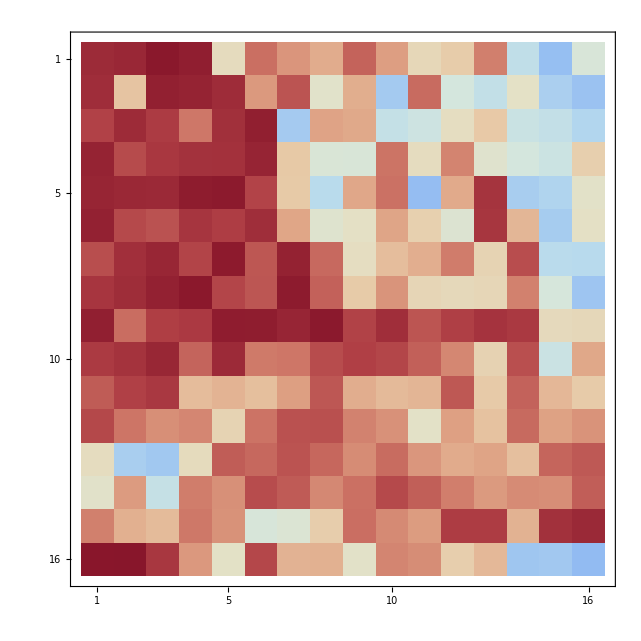

```mathematica
MatrixPlot[bandomoi-.5,ColorFunction->ColorData["ThermometerColors"]]
```

Make another actual plot in the same size of the plot above to have some visual comparison:

```mathematica
GeoGraphics[GeoDestination[GeoDestination[vitri,{60000,90}],{60000,180}],GeoRange->LinguisticAssistant,ImageSize->Large]
```

-Graphics-

Smooth Plot in a Small Part of Vietnam

Collecting Locations of 4 point s forming a rectangle:

```mathematica
point1=GeoPosition[{11.111457,107.636774}]
```

GeoPosition[{11.1115,107.637}]

```mathematica
point2=GeoPosition[{11.111457,109.803591}]
```

GeoPosition[{11.1115,109.804}]

```mathematica
point3=GeoPosition[{8.991341,107.636774}]
```

GeoPosition[{8.99134,107.637}]

```mathematica
point4=GeoPosition[{8.991341,109.803591}]
```

GeoPosition[{8.99134,109.804}]

Measuring the width of the rectangle:

```mathematica
rong=UnitConvert[GeoDistance[point1,point2],LinguisticAssistant]//QuantityMagnitude
```

236716.

Measuring the length of the rectangle :

```mathematica
dai=UnitConvert[GeoDistance[point1,point3],LinguisticAssistant]//QuantityMagnitude
```

234502.

Calculating the numbers of jumping steps on the width:

```mathematica
soluongbuocnhayngang=rong/8000+1//Floor
```

30

Calculating the number of jumping steps on the length:

```mathematica
soluongbuocnhaydoc=(dai-8000)/8000+1//Floor
```

29

From Point 1, move to its right x times for 8000 meters in each step to get a list of new coordinates whereas x is the number of  jumping steps on the width:

```mathematica
vitringang1=Table[GeoDestination[GeoPosition[point1],{dist,90}],{dist,0,rong,8000}]
```

{GeoPosition[{11.1115,107.637}],GeoPosition[{11.1114,107.71}],GeoPosition[{11.1114,107.783}],GeoPosition[{11.1114,107.856}],GeoPosition[{11.1113,107.93}],GeoPosition[{11.1112,108.003}],GeoPosition[{11.1111,108.076}],GeoPosition[{11.111,108.149}],GeoPosition[{11.1109,108.223}],GeoPosition[{11.1107,108.296}],GeoPosition[{11.1106,108.369}],GeoPosition[{11.1104,108.442}],GeoPosition[{11.1102,108.516}],GeoPosition[{11.11,108.589}],GeoPosition[{11.1097,108.662}],GeoPosition[{11.1095,108.735}],GeoPosition[{11.1092,108.808}],GeoPosition[{11.1089,108.882}],GeoPosition[{11.1086,108.955}],GeoPosition[{11.1082,109.028}],GeoPosition[{11.1079,109.101}],GeoPosition[{11.1075,109.175}],GeoPosition[{11.1071,109.248}],GeoPosition[{11.1067,109.321}],GeoPosition[{11.1063,109.394}],GeoPosition[{11.1059,109.467}],GeoPosition[{11.1054,109.541}],GeoPosition[{11.105,109.614}],GeoPosition[{11.1045,109.687}],GeoPosition[{11.104,109.76}]}

From each point from the list above, move downwards y times for 8000 meters in each step to get a list of new coordinates whereas y is the number of  jumping steps on the length:

```mathematica
vitridoc1= Table[GeoDestination[GeoPosition[#],{dist,180}],{dist,8000,dai,8000}]&/@vitringang1
```

Have to rearrange the list of coordinates vertical instead of horizontal:

```mathematica
vitridoc1dachinhsua=Table[vitridoc1[[All,n]],{n,1,soluongbuocnhaydoc}];
```

Join the lists of coordinates above all together into a big list:

```mathematica
tatcavitri1=Join[vitridoc1dachinhsua,vitringang1]//Flatten;
```

Make a list of plots for each coordinate in the list above:

```mathematica
bando1=ReliefPlot[Reverse[GeoElevationData[{#,{(#/.GeoPosition[x_]->x)[[1]]-0.05,(#/.GeoPosition[x_]->x)[[2]]+0.05}},GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic,GeoCenter->Automatic]],ImageSize->Medium,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None]&/@(GeoPosition/@tatcavitri1);
```

For each plot, apply the Final Function the get the Probability of Land and Water:

```mathematica
topo11=predictor[#]&/@bando1//Flatten
```

{Land→0.0648812,Sea→0.935119,Land→0.8693,Sea→0.1307,Land→0.747386,Sea→0.252614,Land→0.979053,Sea→0.0209466,Land→0.909771,Sea→0.0902294,Land→0.658302,Sea→0.341698,Land→0.584557,Sea→0.415443,Land→0.209555,Sea→0.790445,Land→0.793342,Sea→0.206658,Land→0.960776,Sea→0.039224,Land→0.893827,Sea→0.106173,Land→0.326672,Sea→0.673328,Land→0.749542,Sea→0.250458,Land→0.639782,Sea→0.360218,Land→0.88836,Sea→0.11164,Land→0.64178,Sea→0.35822,Land→0.607043,Sea→0.392957,Land→0.133832,Sea→0.866168,Land→0.763907,Sea→0.236093,Land→0.250865,Sea→0.749135,Land→0.844585,Sea→0.155415,Land→0.365844,Sea→0.634156,Land→0.232213,Sea→0.767787,Land→0.892818,Sea→0.107182,Land→0.285094,Sea→0.714906,Land→0.309547,Sea→0.690453,Land→0.0352646,Sea→0.964735,Land→0.109254,Sea→0.890746,Land→0.136434,Sea→0.863566,Land→0.0567716,Sea→0.943228,Land→0.851497,Sea→0.148503,Land→0.79521,Sea→0.20479,Land→0.990523,Sea→0.00947744,Land→0.848376,Sea→0.151624,Land→0.591604,Sea→0.408396,Land→0.250235,Sea→0.749765,Land→0.98812,Sea→0.0118796,Land→0.833419,Sea→0.166581,Land→0.848511,Sea→0.151489,Land→0.981935,Sea→0.0180652,Land→0.293798,Sea→0.706202,Land→0.851976,Sea→0.148024,Land→0.460135,Sea→0.539865,Land→0.919451,Sea→0.080549,Land→0.580235,Sea→0.419765,Land→0.552646,Sea→0.447354,Land→0.559404,Sea→0.440596,Land→0.749619,Sea→0.250381,Land→0.655122,Sea→0.344878,Land→0.41733,Sea→0.58267,Land→0.231753,Sea→0.768247,Land→0.0390495,Sea→0.96095,Land→0.837583,Sea→0.162417,Land→0.78012,Sea→0.21988,Land→0.498191,Sea→0.501809,Land→0.282126,Sea→0.717874,Land→0.12236,Sea→0.87764,Land→0.0224099,Sea→0.97759,Land→0.0937818,Sea→0.906218,Land→0.0209106,Sea→0.979089,Land→0.784978,Sea→0.215022,Land→0.911052,Sea→0.0889484,Land→0.993954,Sea→0.00604641,Land→0.970416,Sea→0.0295844,Land→0.765432,Sea→0.234568,Land→0.976975,Sea→0.0230252,Land→0.660956,Sea→0.339044,Land→0.542517,Sea→0.457483,Land→0.738577,Sea→0.261423,Land→0.460357,Sea→0.539643,Land→0.545383,Sea→0.454617,Land→0.897862,Sea→0.102138,Land→0.93634,Sea→0.0636599,Land→0.782513,Sea→0.217487,Land→0.462282,Sea→0.537718,Land→0.529289,Sea→0.470711,Land→0.702109,Sea→0.297891,Land→0.742536,Sea→0.257464,Land→0.97195,Sea→0.0280495,Land→0.169616,Sea→0.830384,Land→0.805085,Sea→0.194915,Land→0.95144,Sea→0.0485602,Land→0.239231,Sea→0.760769,Land→0.117077,Sea→0.882923,Land→0.139904,Sea→0.860096,Land→0.124449,Sea→0.875551,Land→0.0283503,Sea→0.97165,Land→0.0874766,Sea→0.912523,Land→0.176456,Sea→0.823544,Land→0.0875106,Sea→0.912489,Land→0.430409,Sea→0.569591,Land→0.720126,Sea→0.279874,Land→0.9653,Sea→0.0346999,Land→0.168998,Sea→0.831002,Land→0.12929,Sea→0.87071,Land→0.967219,Sea→0.0327806,Land→0.0916934,Sea→0.908307,Land→0.577653,Sea→0.422347,Land→0.38729,Sea→0.61271,Land→0.846027,Sea→0.153973,Land→0.606211,Sea→0.393789,Land→0.814396,Sea→0.185604,Land→0.383069,Sea→0.616931,Land→0.516313,Sea→0.483687,Land→0.546307,Sea→0.453693,Land→0.636429,Sea→0.363571,Land→0.771636,Sea→0.228364,Land→0.259826,Sea→0.740174,Land→0.693373,Sea→0.306627,Land→0.0890598,Sea→0.91094,Land→0.907114,Sea→0.0928862,Land→0.938367,Sea→0.0616329,Land→0.338238,Sea→0.661762,Land→0.142028,Sea→0.857972,Land→0.0331115,Sea→0.966889,Land→0.280406,Sea→0.719594,Land→0.0294739,Sea→0.970526,Land→0.0716211,Sea→0.928379,Land→0.116646,Sea→0.883354,Land→0.247114,Sea→0.752886,Land→0.934113,Sea→0.065887,Land→0.0634862,Sea→0.936514,Land→0.457329,Sea→0.542671,Land→0.985074,Sea→0.0149264,Land→0.873232,Sea→0.126768,Land→0.818744,Sea→0.181256,Land→0.69558,Sea→0.30442,Land→0.465556,Sea→0.534444,Land→0.731067,Sea→0.268933,Land→0.650869,Sea→0.349131,Land→0.558526,Sea→0.441474,Land→0.254832,Sea→0.745168,Land→0.798631,Sea→0.201369,Land→0.771594,Sea→0.228406,Land→0.420082,Sea→0.579918,Land→0.377684,Sea→0.622316,Land→0.830898,Sea→0.169102,Land→0.490709,Sea→0.509291,Land→0.165348,Sea→0.834652,Land→0.421869,Sea→0.578131,Land→0.362929,Sea→0.637071,Land→0.675096,Sea→0.324904,Land→0.550929,Sea→0.449071,Land→0.610804,Sea→0.389196,Land→0.0888058,Sea→0.911194,Land→0.0669545,Sea→0.933046,Land→0.0324003,Sea→0.9676,Land→0.270869,Sea→0.729131,Land→0.463543,Sea→0.536457,Land→0.136739,Sea→0.863261,Land→0.855962,Sea→0.144038,Land→0.980389,Sea→0.0196109,Land→0.955362,Sea→0.0446375,Land→0.340028,Sea→0.659972,Land→0.859586,Sea→0.140414,Land→0.348354,Sea→0.651646,Land→0.811498,Sea→0.188502,Land→0.690671,Sea→0.309329,Land→0.710174,Sea→0.289826,Land→0.904904,Sea→0.095096,Land→0.762481,Sea→0.237519,Land→0.92744,Sea→0.07256,Land→0.409128,Sea→0.590872,Land→0.919435,Sea→0.0805651,Land→0.582972,Sea→0.417028,Land→0.531554,Sea→0.468446,Land→0.271581,Sea→0.728419,Land→0.575324,Sea→0.424676,Land→0.397526,Sea→0.602474,Land→0.467934,Sea→0.532066,Land→0.33796,Sea→0.66204,Land→0.605005,Sea→0.394995,Land→0.394945,Sea→0.605055,Land→0.243011,Sea→0.756989,Land→0.129054,Sea→0.870946,Land→0.0355589,Sea→0.964441,Land→0.0860238,Sea→0.913976,Land→0.0293927,Sea→0.970607,Land→0.180007,Sea→0.819993,Land→0.401775,Sea→0.598225,Land→0.937225,Sea→0.0627748,Land→0.221105,Sea→0.778895,Land→0.349186,Sea→0.650814,Land→0.53293,Sea→0.46707,Land→0.532888,Sea→0.467112,Land→0.416449,Sea→0.583551,Land→0.569377,Sea→0.430623,Land→0.852293,Sea→0.147707,Land→0.613028,Sea→0.386972,Land→0.653311,Sea→0.346689,Land→0.472435,Sea→0.527565,Land→0.605734,Sea→0.394266,Land→0.73017,Sea→0.26983,Land→0.610394,Sea→0.389606,Land→0.212863,Sea→0.787137,Land→0.644672,Sea→0.355328,Land→0.944841,Sea→0.0551593,Land→0.891853,Sea→0.108147,Land→0.26695,Sea→0.73305,Land→0.401193,Sea→0.598807,Land→0.38685,Sea→0.61315,Land→0.922862,Sea→0.0771375,Land→0.783926,Sea→0.216074,Land→0.179649,Sea→0.820351,Land→0.1175,Sea→0.8825,Land→0.0361337,Sea→0.963866,Land→0.350892,Sea→0.649108,Land→0.862723,Sea→0.137277,Land→0.519152,Sea→0.480848,Land→0.270269,Sea→0.729731,Land→0.35994,Sea→0.64006,Land→0.788337,Sea→0.211663,Land→0.666592,Sea→0.333408,Land→0.590785,Sea→0.409215,Land→0.544382,Sea→0.455618,Land→0.775745,Sea→0.224255,Land→0.362172,Sea→0.637828,Land→0.848405,Sea→0.151595,Land→0.806592,Sea→0.193408,Land→0.700561,Sea→0.299439,Land→0.863763,Sea→0.136237,Land→0.784705,Sea→0.215295,Land→0.563427,Sea→0.436573,Land→0.973257,Sea→0.0267431,Land→0.830716,Sea→0.169284,Land→0.539884,Sea→0.460116,Land→0.568259,Sea→0.431741,Land→0.500134,Sea→0.499866,Land→0.8816,Sea→0.1184,Land→0.127863,Sea→0.872137,Land→0.678089,Sea→0.321911,Land→0.960089,Sea→0.0399113,Land→0.499483,Sea→0.500517,Land→0.227348,Sea→0.772652,Land→0.042874,Sea→0.957126,Land→0.0684509,Sea→0.931549,Land→0.216726,Sea→0.783274,Land→0.0181544,Sea→0.981846,Land→0.0844266,Sea→0.915573,Land→0.0510255,Sea→0.948974,Land→0.902795,Sea→0.0972049,Land→0.649779,Sea→0.350221,Land→0.578769,Sea→0.421231,Land→0.492955,Sea→0.507045,Land→0.804247,Sea→0.195753,Land→0.536828,Sea→0.463172,Land→0.871199,Sea→0.128801,Land→0.891442,Sea→0.108558,Land→0.687117,Sea→0.312883,Land→0.61396,Sea→0.38604,Land→0.333256,Sea→0.666744,Land→0.863977,Sea→0.136023,Land→0.515044,Sea→0.484956,Land→0.429655,Sea→0.570345,Land→0.590081,Sea→0.409919,Land→0.67201,Sea→0.32799,Land→0.179592,Sea→0.820408,Land→0.42146,Sea→0.57854,Land→0.0844519,Sea→0.915548,Land→0.0397989,Sea→0.960201,Land→0.683509,Sea→0.316491,Land→0.804689,Sea→0.195311,Land→0.294284,Sea→0.705716,Land→0.248523,Sea→0.751477,Land→0.107466,Sea→0.892534,Land→0.059867,Sea→0.940133,Land→0.0245899,Sea→0.97541,Land→0.0848998,Sea→0.9151,Land→0.01342,Sea→0.98658,Land→0.031751,Sea→0.968249,Land→0.468088,Sea→0.531912,Land→0.48011,Sea→0.51989,Land→0.350526,Sea→0.649474,Land→0.936497,Sea→0.0635031,Land→0.827178,Sea→0.172822,Land→0.921831,Sea→0.0781686,Land→0.48148,Sea→0.51852,Land→0.315982,Sea→0.684018,Land→0.634473,Sea→0.365527,Land→0.813083,Sea→0.186917,Land→0.404094,Sea→0.595906,Land→0.623619,Sea→0.376381,Land→0.758781,Sea→0.241219,Land→0.447603,Sea→0.552397,Land→0.129068,Sea→0.870932,Land→0.756373,Sea→0.243627,Land→0.112243,Sea→0.887757,Land→0.19319,Sea→0.80681,Land→0.39772,Sea→0.60228,Land→0.509294,Sea→0.490706,Land→0.0820479,Sea→0.917952,Land→0.0716886,Sea→0.928311,Land→0.324264,Sea→0.675736,Land→0.282786,Sea→0.717214,Land→0.309394,Sea→0.690606,Land→0.215878,Sea→0.784122,Land→0.0585935,Sea→0.941407,Land→0.0465235,Sea→0.953476,Land→0.0628713,Sea→0.937129,Land→0.0233109,Sea→0.976689,Land→0.582709,Sea→0.417291,Land→0.672956,Sea→0.327044,Land→0.612941,Sea→0.387059,Land→0.84976,Sea→0.15024,Land→0.561254,Sea→0.438746,Land→0.653397,Sea→0.346603,Land→0.698766,Sea→0.301234,Land→0.900402,Sea→0.0995983,Land→0.657604,Sea→0.342396,Land→0.795158,Sea→0.204842,Land→0.332158,Sea→0.667842,Land→0.752372,Sea→0.247628,Land→0.722131,Sea→0.277869,Land→0.522633,Sea→0.477367,Land→0.887469,Sea→0.112531,Land→0.87802,Sea→0.12198,Land→0.893404,Sea→0.106596,Land→0.426818,Sea→0.573182,Land→0.0239912,Sea→0.976009,Land→0.104101,Sea→0.895899,Land→0.269994,Sea→0.730006,Land→0.301725,Sea→0.698275,Land→0.0593039,Sea→0.940696,Land→0.0355315,Sea→0.964468,Land→0.0438357,Sea→0.956164,Land→0.0295214,Sea→0.970479,Land→0.350718,Sea→0.649282,Land→0.483361,Sea→0.516639,Land→0.0157348,Sea→0.984265,Land→0.0204157,Sea→0.979584,Land→0.794362,Sea→0.205638,Land→0.842888,Sea→0.157112,Land→0.789821,Sea→0.210179,Land→0.819258,Sea→0.180742,Land→0.5588,Sea→0.4412,Land→0.909934,Sea→0.0900662,Land→0.703583,Sea→0.296417,Land→0.689743,Sea→0.310257,Land→0.1442,Sea→0.8558,Land→0.882038,Sea→0.117962,Land→0.819599,Sea→0.180401,Land→0.973197,Sea→0.0268033,Land→0.365009,Sea→0.634991,Land→0.719121,Sea→0.280879,Land→0.425558,Sea→0.574442,Land→0.805515,Sea→0.194485,Land→0.0658069,Sea→0.934193,Land→0.131131,Sea→0.868869,Land→0.949153,Sea→0.050847,Land→0.0244161,Sea→0.975584,Land→0.0756624,Sea→0.924338,Land→0.0363574,Sea→0.963643,Land→0.275823,Sea→0.724177,Land→0.236339,Sea→0.763661,Land→0.0436489,Sea→0.956351,Land→0.0346169,Sea→0.965383,Land→0.119125,Sea→0.880875,Land→0.0487894,Sea→0.951211,Land→0.0246774,Sea→0.975323,Land→0.0293794,Sea→0.970621,Land→0.9193,Sea→0.0806996,Land→0.933586,Sea→0.0664139,Land→0.766467,Sea→0.233533,Land→0.681451,Sea→0.318549,Land→0.54919,Sea→0.45081,Land→0.678514,Sea→0.321486,Land→0.815814,Sea→0.184186,Land→0.513146,Sea→0.486854,Land→0.282387,Sea→0.717613,Land→0.383615,Sea→0.616385,Land→0.772219,Sea→0.227781,Land→0.261568,Sea→0.738432,Land→0.425439,Sea→0.574561,Land→0.704165,Sea→0.295835,Land→0.748233,Sea→0.251767,Land→0.233342,Sea→0.766658,Land→0.714511,Sea→0.285489,Land→0.67153,Sea→0.32847,Land→0.0260386,Sea→0.973961,Land→0.662568,Sea→0.337432,Land→0.0364448,Sea→0.963555,Land→0.0954043,Sea→0.904596,Land→0.200683,Sea→0.799317,Land→0.0620526,Sea→0.937947,Land→0.0228158,Sea→0.977184,Land→0.0550145,Sea→0.944985,Land→0.116435,Sea→0.883565,Land→0.024106,Sea→0.975894,Land→0.0512692,Sea→0.948731,Land→0.026623,Sea→0.973377,Land→0.580797,Sea→0.419203,Land→0.717547,Sea→0.282453,Land→0.261253,Sea→0.738747,Land→0.597278,Sea→0.402722,Land→0.446103,Sea→0.553897,Land→0.949398,Sea→0.0506025,Land→0.222947,Sea→0.777053,Land→0.342104,Sea→0.657896,Land→0.882159,Sea→0.117841,Land→0.425313,Sea→0.574687,Land→0.554966,Sea→0.445034,Land→0.78181,Sea→0.21819,Land→0.86024,Sea→0.13976,Land→0.498804,Sea→0.501196,Land→0.523586,Sea→0.476414,Land→0.708965,Sea→0.291035,Land→0.640378,Sea→0.359622,Land→0.84101,Sea→0.15899,Land→0.335926,Sea→0.664074,Land→0.392275,Sea→0.607725,Land→0.0360201,Sea→0.96398,Land→0.0570001,Sea→0.943,Land→0.0621897,Sea→0.93781,Land→0.0417011,Sea→0.958299,Land→0.0871177,Sea→0.912882,Land→0.092037,Sea→0.907963,Land→0.0802304,Sea→0.91977,Land→0.025073,Sea→0.974927,Land→0.0179209,Sea→0.982079,Land→0.0167537,Sea→0.983246,Land→0.629006,Sea→0.370994,Land→0.761018,Sea→0.238982,Land→0.895701,Sea→0.104299,Land→0.853597,Sea→0.146403,Land→0.898862,Sea→0.101138,Land→0.713724,Sea→0.286276,Land→0.454821,Sea→0.545179,Land→0.326189,Sea→0.673811,Land→0.119887,Sea→0.880113,Land→0.790584,Sea→0.209416,Land→0.631935,Sea→0.368065,Land→0.919349,Sea→0.0806513,Land→0.632709,Sea→0.367291,Land→0.836883,Sea→0.163117,Land→0.160019,Sea→0.839981,Land→0.73181,Sea→0.26819,Land→0.87477,Sea→0.12523,Land→0.0648386,Sea→0.935161,Land→0.148568,Sea→0.851432,Land→0.0894698,Sea→0.91053,Land→0.0553475,Sea→0.944653,Land→0.0474482,Sea→0.952552,Land→0.0410676,Sea→0.958932,Land→0.0223975,Sea→0.977603,Land→0.12414,Sea→0.87586,Land→0.141719,Sea→0.858281,Land→0.0250284,Sea→0.974972,Land→0.0562258,Sea→0.943774,Land→0.0263361,Sea→0.973664,Land→0.0440292,Sea→0.955971,Land→0.657571,Sea→0.342429,Land→0.903362,Sea→0.0966382,Land→0.840623,Sea→0.159377,Land→0.564963,Sea→0.435037,Land→0.891882,Sea→0.108118,Land→0.778419,Sea→0.221581,Land→0.47048,Sea→0.52952,Land→0.749479,Sea→0.250521,Land→0.769986,Sea→0.230014,Land→0.861286,Sea→0.138714,Land→0.885861,Sea→0.114139,Land→0.951083,Sea→0.0489172,Land→0.403218,Sea→0.596782,Land→0.354415,Sea→0.645585,Land→0.535449,Sea→0.464551,Land→0.555053,Sea→0.444947,Land→0.552822,Sea→0.447178,Land→0.801368,Sea→0.198632,Land→0.207211,Sea→0.792789,Land→0.14685,Sea→0.85315,Land→0.0422299,Sea→0.95777,Land→0.0360108,Sea→0.963989,Land→0.0406559,Sea→0.959344,Land→0.0206824,Sea→0.979318,Land→0.0185966,Sea→0.981403,Land→0.0206258,Sea→0.979374,Land→0.0173049,Sea→0.982695,Land→0.0252937,Sea→0.974706,Land→0.0290174,Sea→0.970983,Land→0.0225171,Sea→0.977483,Land→0.9147,Sea→0.0852999,Land→0.725231,Sea→0.274769,Land→0.672608,Sea→0.327392,Land→0.454462,Sea→0.545538,Land→0.893342,Sea→0.106658,Land→0.904857,Sea→0.0951431,Land→0.861225,Sea→0.138775,Land→0.29695,Sea→0.70305,Land→0.70472,Sea→0.29528,Land→0.174116,Sea→0.825884,Land→0.615665,Sea→0.384335,Land→0.0424779,Sea→0.957522,Land→0.31733,Sea→0.68267,Land→0.595849,Sea→0.404151,Land→0.909994,Sea→0.0900061,Land→0.754679,Sea→0.245321,Land→0.84685,Sea→0.15315,Land→0.553915,Sea→0.446085,Land→0.55863,Sea→0.44137,Land→0.543414,Sea→0.456586,Land→0.0227828,Sea→0.977217,Land→0.0266466,Sea→0.973353,Land→0.0954833,Sea→0.904517,Land→0.0387731,Sea→0.961227,Land→0.0251733,Sea→0.974827,Land→0.0272273,Sea→0.972773,Land→0.0755567,Sea→0.924443,Land→0.0136316,Sea→0.986368,Land→0.0227595,Sea→0.97724,Land→0.0353718,Sea→0.964628,Land→0.701482,Sea→0.298518,Land→0.738869,Sea→0.261131,Land→0.271103,Sea→0.728897,Land→0.691537,Sea→0.308463,Land→0.898783,Sea→0.101217,Land→0.761771,Sea→0.238229,Land→0.832051,Sea→0.167949,Land→0.859958,Sea→0.140042,Land→0.356313,Sea→0.643687,Land→0.504118,Sea→0.495882,Land→0.675256,Sea→0.324744,Land→0.389503,Sea→0.610497,Land→0.446788,Sea→0.553212,Land→0.245155,Sea→0.754845,Land→0.4155,Sea→0.5845,Land→0.138765,Sea→0.861235,Land→0.660615,Sea→0.339385,Land→0.546231,Sea→0.453769,Land→0.848446,Sea→0.151554,Land→0.0270143,Sea→0.972986,Land→0.0295701,Sea→0.97043,Land→0.0837301,Sea→0.91627,Land→0.0258128,Sea→0.974187,Land→0.0234131,Sea→0.976587,Land→0.0411139,Sea→0.958886,Land→0.0249881,Sea→0.975012,Land→0.0199849,Sea→0.980015,Land→0.0674109,Sea→0.932589,Land→0.0221135,Sea→0.977887,Land→0.0141384,Sea→0.985862,Land→0.936929,Sea→0.0630705,Land→0.595023,Sea→0.404977,Land→0.440546,Sea→0.559454,Land→0.569423,Sea→0.430577,Land→0.790147,Sea→0.209853,Land→0.859715,Sea→0.140285,Land→0.170517,Sea→0.829483,Land→0.570608,Sea→0.429392,Land→0.513096,Sea→0.486904,Land→0.439193,Sea→0.560807,Land→0.392036,Sea→0.607964,Land→0.697576,Sea→0.302424,Land→0.270144,Sea→0.729856,Land→0.345447,Sea→0.654553,Land→0.034098,Sea→0.965902,Land→0.512087,Sea→0.487913,Land→0.624343,Sea→0.375657,Land→0.892604,Sea→0.107396,Land→0.451678,Sea→0.548322,Land→0.748565,Sea→0.251435,Land→0.0605499,Sea→0.93945,Land→0.155706,Sea→0.844294,Land→0.0491574,Sea→0.950843,Land→0.0149289,Sea→0.985071,Land→0.00911145,Sea→0.990889,Land→0.0405031,Sea→0.959497,Land→0.010707,Sea→0.989293,Land→0.0174864,Sea→0.982514,Land→0.0500289,Sea→0.949971,Land→0.0267004,Sea→0.9733,Land→0.886062,Sea→0.113938,Land→0.658377,Sea→0.341623,Land→0.47539,Sea→0.52461,Land→0.774141,Sea→0.225859,Land→0.628121,Sea→0.371879,Land→0.204233,Sea→0.795767,Land→0.242799,Sea→0.757201,Land→0.295967,Sea→0.704033,Land→0.0738431,Sea→0.926157,Land→0.610697,Sea→0.389303,Land→0.498249,Sea→0.501751,Land→0.479654,Sea→0.520346,Land→0.262878,Sea→0.737122,Land→0.760037,Sea→0.239963,Land→0.0460306,Sea→0.953969,Land→0.157602,Sea→0.842398,Land→0.626484,Sea→0.373516,Land→0.0917082,Sea→0.908292,Land→0.400835,Sea→0.599165,Land→0.263837,Sea→0.736163,Land→0.0848937,Sea→0.915106,Land→0.0412091,Sea→0.958791,Land→0.0260501,Sea→0.97395,Land→0.0288204,Sea→0.97118,Land→0.0207878,Sea→0.979212,Land→0.0273621,Sea→0.972638,Land→0.0832501,Sea→0.91675,Land→0.0214622,Sea→0.978538,Land→0.017613,Sea→0.982387,Land→0.0248873,Sea→0.975113,Land→0.780715,Sea→0.219285,Land→0.841089,Sea→0.158911,Land→0.44419,Sea→0.55581,Land→0.45522,Sea→0.54478,Land→0.451162,Sea→0.548838,Land→0.652289,Sea→0.347711,Land→0.632928,Sea→0.367072,Land→0.0231141,Sea→0.976886,Land→0.207363,Sea→0.792637,Land→0.835118,Sea→0.164882,Land→0.691947,Sea→0.308053,Land→0.4883,Sea→0.5117,Land→0.42135,Sea→0.57865,Land→0.896279,Sea→0.103721,Land→0.230118,Sea→0.769882,Land→0.734687,Sea→0.265313,Land→0.198142,Sea→0.801858,Land→0.237194,Sea→0.762806,Land→0.561373,Sea→0.438627,Land→0.985451,Sea→0.0145494,Land→0.0168289,Sea→0.983171,Land→0.0169293,Sea→0.983071,Land→0.020165,Sea→0.979835,Land→0.0142585,Sea→0.985742,Land→0.0314313,Sea→0.968569,Land→0.0510289,Sea→0.948971,Land→0.0242024,Sea→0.975798,Land→0.050525,Sea→0.949475,Land→0.0269606,Sea→0.973039,Land→0.0359853,Sea→0.964015,Land→0.322097,Sea→0.677903,Land→0.86166,Sea→0.13834,Land→0.701515,Sea→0.298485,Land→0.233295,Sea→0.766705,Land→0.733971,Sea→0.266029,Land→0.513033,Sea→0.486967,Land→0.612451,Sea→0.387549,Land→0.508194,Sea→0.491806,Land→0.991198,Sea→0.00880211,Land→0.678839,Sea→0.321161,Land→0.927959,Sea→0.0720405,Land→0.850481,Sea→0.149519,Land→0.842458,Sea→0.157542,Land→0.431845,Sea→0.568155,Land→0.748213,Sea→0.251787,Land→0.326733,Sea→0.673267,Land→0.768383,Sea→0.231617,Land→0.920706,Sea→0.0792936,Land→0.454627,Sea→0.545373,Land→0.0397489,Sea→0.960251,Land→0.0176941,Sea→0.982306,Land→0.0268506,Sea→0.973149,Land→0.0337183,Sea→0.966282,Land→0.020699,Sea→0.979301,Land→0.0116776,Sea→0.988322,Land→0.0846395,Sea→0.91536,Land→0.0175813,Sea→0.982419,Land→0.0256035,Sea→0.974397,Land→0.0298348,Sea→0.970165,Land→0.0280727,Sea→0.971927,Land→0.434045,Sea→0.565955,Land→0.896147,Sea→0.103853,Land→0.343742,Sea→0.656258,Land→0.576576,Sea→0.423424,Land→0.501682,Sea→0.498318,Land→0.484389,Sea→0.515611,Land→0.0858914,Sea→0.914109,Land→0.0303458,Sea→0.969654,Land→0.419424,Sea→0.580576,Land→0.574747,Sea→0.425253,Land→0.381321,Sea→0.618679,Land→0.50812,Sea→0.49188,Land→0.924327,Sea→0.0756726,Land→0.142781,Sea→0.857219,Land→0.650716,Sea→0.349284,Land→0.361717,Sea→0.638283,Land→0.06631,Sea→0.93369,Land→0.542136,Sea→0.457864,Land→0.0930525,Sea→0.906947,Land→0.0270285,Sea→0.972972,Land→0.0271264,Sea→0.972874,Land→0.0246225,Sea→0.975378,Land→0.0401501,Sea→0.95985,Land→0.0247512,Sea→0.975249,Land→0.0164598,Sea→0.98354,Land→0.0478908,Sea→0.952109,Land→0.157644,Sea→0.842356,Land→0.0305192,Sea→0.969481,Land→0.0217474,Sea→0.978253,Land→0.0332708,Sea→0.966729,Land→0.719022,Sea→0.280978,Land→0.542206,Sea→0.457794,Land→0.562515,Sea→0.437485,Land→0.568258,Sea→0.431742,Land→0.951044,Sea→0.0489563,Land→0.621814,Sea→0.378186,Land→0.381919,Sea→0.618081,Land→0.0985002,Sea→0.9015,Land→0.754623,Sea→0.245377,Land→0.907216,Sea→0.0927843,Land→0.172329,Sea→0.827671,Land→0.128078,Sea→0.871922,Land→0.245681,Sea→0.754319,Land→0.0415474,Sea→0.958453,Land→0.199845,Sea→0.800155,Land→0.417805,Sea→0.582195,Land→0.476077,Sea→0.523923,Land→0.258526,Sea→0.741474,Land→0.106757,Sea→0.893243,Land→0.0530666,Sea→0.946933,Land→0.054189,Sea→0.945811,Land→0.0436107,Sea→0.956389,Land→0.0286053,Sea→0.971395,Land→0.0372176,Sea→0.962782,Land→0.0375786,Sea→0.962421,Land→0.0707215,Sea→0.929279,Land→0.0157597,Sea→0.98424,Land→0.0748253,Sea→0.925175,Land→0.0369044,Sea→0.963096,Land→0.0722243,Sea→0.927776,Land→0.526428,Sea→0.473572,Land→0.358375,Sea→0.641625,Land→0.489705,Sea→0.510295,Land→0.697752,Sea→0.302248,Land→0.317426,Sea→0.682574,Land→0.96309,Sea→0.0369102,Land→0.925707,Sea→0.0742925,Land→0.342446,Sea→0.657554,Land→0.55784,Sea→0.44216,Land→0.847847,Sea→0.152153,Land→0.233576,Sea→0.766424,Land→0.764755,Sea→0.235245,Land→0.777996,Sea→0.222004,Land→0.675418,Sea→0.324582,Land→0.886816,Sea→0.113184,Land→0.939898,Sea→0.0601021,Land→0.253284,Sea→0.746716,Land→0.0373322,Sea→0.962668,Land→0.215574,Sea→0.784426,Land→0.0773048,Sea→0.922695,Land→0.0769434,Sea→0.923057,Land→0.0254528,Sea→0.974547,Land→0.0246596,Sea→0.97534,Land→0.0315634,Sea→0.968437,Land→0.0279707,Sea→0.972029,Land→0.0477098,Sea→0.95229,Land→0.0556687,Sea→0.944331,Land→0.0279035,Sea→0.972096,Land→0.0439015,Sea→0.956099,Land→0.0177062,Sea→0.982294,Land→0.588105,Sea→0.411895,Land→0.920893,Sea→0.0791075,Land→0.232378,Sea→0.767622,Land→0.652791,Sea→0.347209,Land→0.693433,Sea→0.306567,Land→0.773304,Sea→0.226696,Land→0.372443,Sea→0.627557,Land→0.837569,Sea→0.162431,Land→0.549785,Sea→0.450215,Land→0.781243,Sea→0.218757,Land→0.909963,Sea→0.0900369,Land→0.685671,Sea→0.314329,Land→0.215566,Sea→0.784434,Land→0.14141,Sea→0.85859,Land→0.774559,Sea→0.225441,Land→0.708634,Sea→0.291366,Land→0.473787,Sea→0.526213,Land→0.436382,Sea→0.563618,Land→0.812219,Sea→0.187781,Land→0.413548,Sea→0.586452,Land→0.161452,Sea→0.838548,Land→0.0236381,Sea→0.976362,Land→0.0277861,Sea→0.972214,Land→0.0183735,Sea→0.981627,Land→0.0224244,Sea→0.977576,Land→0.0291228,Sea→0.970877,Land→0.0364122,Sea→0.963588,Land→0.0333643,Sea→0.966636,Land→0.0295427,Sea→0.970457,Land→0.015143,Sea→0.984857,Land→0.629411,Sea→0.370589,Land→0.539741,Sea→0.460259,Land→0.865925,Sea→0.134075,Land→0.694669,Sea→0.305331,Land→0.84235,Sea→0.15765,Land→0.422241,Sea→0.577759,Land→0.453889,Sea→0.546111,Land→0.771602,Sea→0.228398,Land→0.556658,Sea→0.443342,Land→0.735675,Sea→0.264325,Land→0.136218,Sea→0.863782,Land→0.233206,Sea→0.766794,Land→0.0985959,Sea→0.901404,Land→0.150708,Sea→0.849292,Land→0.696792,Sea→0.303208,Land→0.327079,Sea→0.672921,Land→0.102951,Sea→0.897049,Land→0.702088,Sea→0.297912,Land→0.0165685,Sea→0.983431,Land→0.0631132,Sea→0.936887,Land→0.148026,Sea→0.851974,Land→0.0186849,Sea→0.981315,Land→0.0225465,Sea→0.977454,Land→0.0308681,Sea→0.969132,Land→0.0284179,Sea→0.971582,Land→0.0210307,Sea→0.978969,Land→0.0506557,Sea→0.949344,Land→0.119747,Sea→0.880253,Land→0.034948,Sea→0.965052,Land→0.065076,Sea→0.934924,Land→0.6269,Sea→0.3731,Land→0.772142,Sea→0.227858,Land→0.854374,Sea→0.145626,Land→0.845674,Sea→0.154326,Land→0.322026,Sea→0.677974,Land→0.815179,Sea→0.184821,Land→0.741593,Sea→0.258407,Land→0.914275,Sea→0.0857248,Land→0.841041,Sea→0.158959,Land→0.665335,Sea→0.334665,Land→0.869458,Sea→0.130542,Land→0.20097,Sea→0.79903,Land→0.580992,Sea→0.419008,Land→0.399473,Sea→0.600527,Land→0.54913,Sea→0.45087,Land→0.970103,Sea→0.0298965,Land→0.842961,Sea→0.157039,Land→0.3528,Sea→0.6472,Land→0.42091,Sea→0.57909,Land→0.0890265,Sea→0.910974,Land→0.021535,Sea→0.978465,Land→0.0376627,Sea→0.962337,Land→0.0221229,Sea→0.977877,Land→0.0276138,Sea→0.972386,Land→0.0317322,Sea→0.968268,Land→0.0114644,Sea→0.988536,Land→0.0176373,Sea→0.982363,Land→0.0314427,Sea→0.968557,Land→0.0227762,Sea→0.977224,Land→0.0216674,Sea→0.978333,Land→0.73488,Sea→0.26512,Land→0.816603,Sea→0.183397,Land→0.911419,Sea→0.088581,Land→0.647927,Sea→0.352073,Land→0.942764,Sea→0.0572363,Land→0.900113,Sea→0.0998868,Land→0.39072,Sea→0.60928,Land→0.864239,Sea→0.135761,Land→0.0945415,Sea→0.905459,Land→0.552317,Sea→0.447683,Land→0.923613,Sea→0.0763865,Land→0.676125,Sea→0.323875,Land→0.505964,Sea→0.494036,Land→0.505919,Sea→0.494081,Land→0.911373,Sea→0.0886269,Land→0.70713,Sea→0.29287,Land→0.520685,Sea→0.479315,Land→0.770098,Sea→0.229902,Land→0.461909,Sea→0.538091,Land→0.117419,Sea→0.882581,Land→0.0237499,Sea→0.97625,Land→0.052424,Sea→0.947576,Land→0.0554825,Sea→0.944518,Land→0.0330914,Sea→0.966909,Land→0.0255312,Sea→0.974469,Land→0.00833044,Sea→0.99167,Land→0.0198632,Sea→0.980137,Land→0.0309303,Sea→0.96907,Land→0.0497488,Sea→0.950251,Land→0.027408,Sea→0.972592,Land→0.25526,Sea→0.74474,Land→0.15645,Sea→0.84355,Land→0.664077,Sea→0.335923,Land→0.986987,Sea→0.0130127,Land→0.956802,Sea→0.0431976,Land→0.915737,Sea→0.0842634,Land→0.152663,Sea→0.847337,Land→0.824799,Sea→0.175201,Land→0.942327,Sea→0.0576726,Land→0.997344,Sea→0.00265593,Land→0.988346,Sea→0.011654,Land→0.964759,Sea→0.0352414,Land→0.238034,Sea→0.761966,Land→0.69943,Sea→0.30057,Land→0.651324,Sea→0.348676,Land→0.46867,Sea→0.53133,Land→0.7934,Sea→0.2066,Land→0.355271,Sea→0.644729,Land→0.415472,Sea→0.584528,Land→0.158478,Sea→0.841522,Land→0.215922,Sea→0.784078,Land→0.44611,Sea→0.55389,Land→0.375664,Sea→0.624336,Land→0.63871,Sea→0.36129,Land→0.235756,Sea→0.764244,Land→0.0921915,Sea→0.907808,Land→0.0726611,Sea→0.927339,Land→0.296459,Sea→0.703541,Land→0.0635757,Sea→0.936424,Land→0.203379,Sea→0.796621}

Collect all the Land Probability of each plot and Arrange them into a  big matrix  :

```mathematica
bandomoi1=Partition[Values[topo11][[#]]&/@Flatten[Position[Keys[topo11],"Land"]],soluongbuocnhayngang]//Flatten
```

{0.0648812,0.8693,0.747386,0.979053,0.909771,0.658302,0.584557,0.209555,0.793342,0.960776,0.893827,0.326672,0.749542,0.639782,0.88836,0.64178,0.607043,0.133832,0.763907,0.250865,0.844585,0.365844,0.232213,0.892818,0.285094,0.309547,0.0352646,0.109254,0.136434,0.0567716,0.851497,0.79521,0.990523,0.848376,0.591604,0.250235,0.98812,0.833419,0.848511,0.981935,0.293798,0.851976,0.460135,0.919451,0.580235,0.552646,0.559404,0.749619,0.655122,0.41733,0.231753,0.0390495,0.837583,0.78012,0.498191,0.282126,0.12236,0.0224099,0.0937818,0.0209106,0.784978,0.911052,0.993954,0.970416,0.765432,0.976975,0.660956,0.542517,0.738577,0.460357,0.545383,0.897862,0.93634,0.782513,0.462282,0.529289,0.702109,0.742536,0.97195,0.169616,0.805085,0.95144,0.239231,0.117077,0.139904,0.124449,0.0283503,0.0874766,0.176456,0.0875106,0.430409,0.720126,0.9653,0.168998,0.12929,0.967219,0.0916934,0.577653,0.38729,0.846027,0.606211,0.814396,0.383069,0.516313,0.546307,0.636429,0.771636,0.259826,0.693373,0.0890598,0.907114,0.938367,0.338238,0.142028,0.0331115,0.280406,0.0294739,0.0716211,0.116646,0.247114,0.934113,0.0634862,0.457329,0.985074,0.873232,0.818744,0.69558,0.465556,0.731067,0.650869,0.558526,0.254832,0.798631,0.771594,0.420082,0.377684,0.830898,0.490709,0.165348,0.421869,0.362929,0.675096,0.550929,0.610804,0.0888058,0.0669545,0.0324003,0.270869,0.463543,0.136739,0.855962,0.980389,0.955362,0.340028,0.859586,0.348354,0.811498,0.690671,0.710174,0.904904,0.762481,0.92744,0.409128,0.919435,0.582972,0.531554,0.271581,0.575324,0.397526,0.467934,0.33796,0.605005,0.394945,0.243011,0.129054,0.0355589,0.0860238,0.0293927,0.180007,0.401775,0.937225,0.221105,0.349186,0.53293,0.532888,0.416449,0.569377,0.852293,0.613028,0.653311,0.472435,0.605734,0.73017,0.610394,0.212863,0.644672,0.944841,0.891853,0.26695,0.401193,0.38685,0.922862,0.783926,0.179649,0.1175,0.0361337,0.350892,0.862723,0.519152,0.270269,0.35994,0.788337,0.666592,0.590785,0.544382,0.775745,0.362172,0.848405,0.806592,0.700561,0.863763,0.784705,0.563427,0.973257,0.830716,0.539884,0.568259,0.500134,0.8816,0.127863,0.678089,0.960089,0.499483,0.227348,0.042874,0.0684509,0.216726,0.0181544,0.0844266,0.0510255,0.902795,0.649779,0.578769,0.492955,0.804247,0.536828,0.871199,0.891442,0.687117,0.61396,0.333256,0.863977,0.515044,0.429655,0.590081,0.67201,0.179592,0.42146,0.0844519,0.0397989,0.683509,0.804689,0.294284,0.248523,0.107466,0.059867,0.0245899,0.0848998,0.01342,0.031751,0.468088,0.48011,0.350526,0.936497,0.827178,0.921831,0.48148,0.315982,0.634473,0.813083,0.404094,0.623619,0.758781,0.447603,0.129068,0.756373,0.112243,0.19319,0.39772,0.509294,0.0820479,0.0716886,0.324264,0.282786,0.309394,0.215878,0.0585935,0.0465235,0.0628713,0.0233109,0.582709,0.672956,0.612941,0.84976,0.561254,0.653397,0.698766,0.900402,0.657604,0.795158,0.332158,0.752372,0.722131,0.522633,0.887469,0.87802,0.893404,0.426818,0.0239912,0.104101,0.269994,0.301725,0.0593039,0.0355315,0.0438357,0.0295214,0.350718,0.483361,0.0157348,0.0204157,0.794362,0.842888,0.789821,0.819258,0.5588,0.909934,0.703583,0.689743,0.1442,0.882038,0.819599,0.973197,0.365009,0.719121,0.425558,0.805515,0.0658069,0.131131,0.949153,0.0244161,0.0756624,0.0363574,0.275823,0.236339,0.0436489,0.0346169,0.119125,0.0487894,0.0246774,0.0293794,0.9193,0.933586,0.766467,0.681451,0.54919,0.678514,0.815814,0.513146,0.282387,0.383615,0.772219,0.261568,0.425439,0.704165,0.748233,0.233342,0.714511,0.67153,0.0260386,0.662568,0.0364448,0.0954043,0.200683,0.0620526,0.0228158,0.0550145,0.116435,0.024106,0.0512692,0.026623,0.580797,0.717547,0.261253,0.597278,0.446103,0.949398,0.222947,0.342104,0.882159,0.425313,0.554966,0.78181,0.86024,0.498804,0.523586,0.708965,0.640378,0.84101,0.335926,0.392275,0.0360201,0.0570001,0.0621897,0.0417011,0.0871177,0.092037,0.0802304,0.025073,0.0179209,0.0167537,0.629006,0.761018,0.895701,0.853597,0.898862,0.713724,0.454821,0.326189,0.119887,0.790584,0.631935,0.919349,0.632709,0.836883,0.160019,0.73181,0.87477,0.0648386,0.148568,0.0894698,0.0553475,0.0474482,0.0410676,0.0223975,0.12414,0.141719,0.0250284,0.0562258,0.0263361,0.0440292,0.657571,0.903362,0.840623,0.564963,0.891882,0.778419,0.47048,0.749479,0.769986,0.861286,0.885861,0.951083,0.403218,0.354415,0.535449,0.555053,0.552822,0.801368,0.207211,0.14685,0.0422299,0.0360108,0.0406559,0.0206824,0.0185966,0.0206258,0.0173049,0.0252937,0.0290174,0.0225171,0.9147,0.725231,0.672608,0.454462,0.893342,0.904857,0.861225,0.29695,0.70472,0.174116,0.615665,0.0424779,0.31733,0.595849,0.909994,0.754679,0.84685,0.553915,0.55863,0.543414,0.0227828,0.0266466,0.0954833,0.0387731,0.0251733,0.0272273,0.0755567,0.0136316,0.0227595,0.0353718,0.701482,0.738869,0.271103,0.691537,0.898783,0.761771,0.832051,0.859958,0.356313,0.504118,0.675256,0.389503,0.446788,0.245155,0.4155,0.138765,0.660615,0.546231,0.848446,0.0270143,0.0295701,0.0837301,0.0258128,0.0234131,0.0411139,0.0249881,0.0199849,0.0674109,0.0221135,0.0141384,0.936929,0.595023,0.440546,0.569423,0.790147,0.859715,0.170517,0.570608,0.513096,0.439193,0.392036,0.697576,0.270144,0.345447,0.034098,0.512087,0.624343,0.892604,0.451678,0.748565,0.0605499,0.155706,0.0491574,0.0149289,0.00911145,0.0405031,0.010707,0.0174864,0.0500289,0.0267004,0.886062,0.658377,0.47539,0.774141,0.628121,0.204233,0.242799,0.295967,0.0738431,0.610697,0.498249,0.479654,0.262878,0.760037,0.0460306,0.157602,0.626484,0.0917082,0.400835,0.263837,0.0848937,0.0412091,0.0260501,0.0288204,0.0207878,0.0273621,0.0832501,0.0214622,0.017613,0.0248873,0.780715,0.841089,0.44419,0.45522,0.451162,0.652289,0.632928,0.0231141,0.207363,0.835118,0.691947,0.4883,0.42135,0.896279,0.230118,0.734687,0.198142,0.237194,0.561373,0.985451,0.0168289,0.0169293,0.020165,0.0142585,0.0314313,0.0510289,0.0242024,0.050525,0.0269606,0.0359853,0.322097,0.86166,0.701515,0.233295,0.733971,0.513033,0.612451,0.508194,0.991198,0.678839,0.927959,0.850481,0.842458,0.431845,0.748213,0.326733,0.768383,0.920706,0.454627,0.0397489,0.0176941,0.0268506,0.0337183,0.020699,0.0116776,0.0846395,0.0175813,0.0256035,0.0298348,0.0280727,0.434045,0.896147,0.343742,0.576576,0.501682,0.484389,0.0858914,0.0303458,0.419424,0.574747,0.381321,0.50812,0.924327,0.142781,0.650716,0.361717,0.06631,0.542136,0.0930525,0.0270285,0.0271264,0.0246225,0.0401501,0.0247512,0.0164598,0.0478908,0.157644,0.0305192,0.0217474,0.0332708,0.719022,0.542206,0.562515,0.568258,0.951044,0.621814,0.381919,0.0985002,0.754623,0.907216,0.172329,0.128078,0.245681,0.0415474,0.199845,0.417805,0.476077,0.258526,0.106757,0.0530666,0.054189,0.0436107,0.0286053,0.0372176,0.0375786,0.0707215,0.0157597,0.0748253,0.0369044,0.0722243,0.526428,0.358375,0.489705,0.697752,0.317426,0.96309,0.925707,0.342446,0.55784,0.847847,0.233576,0.764755,0.777996,0.675418,0.886816,0.939898,0.253284,0.0373322,0.215574,0.0773048,0.0769434,0.0254528,0.0246596,0.0315634,0.0279707,0.0477098,0.0556687,0.0279035,0.0439015,0.0177062,0.588105,0.920893,0.232378,0.652791,0.693433,0.773304,0.372443,0.837569,0.549785,0.781243,0.909963,0.685671,0.215566,0.14141,0.774559,0.708634,0.473787,0.436382,0.812219,0.413548,0.161452,0.0236381,0.0277861,0.0183735,0.0224244,0.0291228,0.0364122,0.0333643,0.0295427,0.015143,0.629411,0.539741,0.865925,0.694669,0.84235,0.422241,0.453889,0.771602,0.556658,0.735675,0.136218,0.233206,0.0985959,0.150708,0.696792,0.327079,0.102951,0.702088,0.0165685,0.0631132,0.148026,0.0186849,0.0225465,0.0308681,0.0284179,0.0210307,0.0506557,0.119747,0.034948,0.065076,0.6269,0.772142,0.854374,0.845674,0.322026,0.815179,0.741593,0.914275,0.841041,0.665335,0.869458,0.20097,0.580992,0.399473,0.54913,0.970103,0.842961,0.3528,0.42091,0.0890265,0.021535,0.0376627,0.0221229,0.0276138,0.0317322,0.0114644,0.0176373,0.0314427,0.0227762,0.0216674,0.73488,0.816603,0.911419,0.647927,0.942764,0.900113,0.39072,0.864239,0.0945415,0.552317,0.923613,0.676125,0.505964,0.505919,0.911373,0.70713,0.520685,0.770098,0.461909,0.117419,0.0237499,0.052424,0.0554825,0.0330914,0.0255312,0.00833044,0.0198632,0.0309303,0.0497488,0.027408,0.25526,0.15645,0.664077,0.986987,0.956802,0.915737,0.152663,0.824799,0.942327,0.997344,0.988346,0.964759,0.238034,0.69943,0.651324,0.46867,0.7934,0.355271,0.415472,0.158478,0.215922,0.44611,0.375664,0.63871,0.235756,0.0921915,0.0726611,0.296459,0.0635757,0.203379}

Make a list of Geographic Positions maps to its Land Probability:

```mathematica
kethopvitrichiso=MapThread[Rule,{tatcavitri1,bandomoi1}];
```

Base on the list above, generate a Geographic Smooth Plot:

```mathematica
GeoSmoothHistogram[kethopvitrichiso,ColorFunction->ColorData["ThermometerColors"]]
```

-Graphics-

## Summary

To summarize, in the first step, I collected the topographies from both on-land and underwater. Then in the second one, the most complicated step, I had tried to use Discrete Fourier Transform (DFT) for a topography image into the matrix, but the problem was that all fourier images were very similar. Then I tried applying a high frequency filter on the images. High frequency filtered output were easy to distinguish since surface above water is generally rough when compared to the surface under water.  After the Image Processing Step, I created the two set of training sets, one is on-land training set and another one is underwater features training set. Hence, I went straight to build the classify function and the Final Function to Return Probabilities of “Land” and “Sea” as well. Finally, for an extra challenge also an nice application in other words for my project, I generated a Temperature Map of a part of Boston and tried to compare it to the actual map and the generated heatmap is similar to the real map.

## Future Work

As we can see, from an arbitrary relief plot of a location, it is possible to turn the relief one into the thermometer surface where blue represents “Sea” and red represents “Land” by using the probabilities that the classifier returned. The first thing that needs to be done is to think of other crucial parameters that can be used, like water bodies around buildings, etc. to increase the accuracy. After increasing the accuracy and interesting thing to do would be to analyze the topography of other celestial bodies (like Mars) and then predict regions where liquids flowed on the surface.